# Quark-gluon vertex SDE

## This program calculates the kernels for diagrams A and B as referenced in Eq. (4.10) of the thesis.

Gustavo L. Teixeira

## Details and definitions

### Constants and rules

Set directory, clear all, and load package X, CSEFort and Matex:

```mathematica
SetDirectory[NotebookDirectory[]];
Clear["Global`*"];
<<X`
<<CSEFort`
<<MaTeX`
```

Package-X v2.1.1 [patched 22/08/2020], by Hiren H. Patel
For more information, see the

Useful rules  - general kinematics:

```mathematica
RuleEuc = {k.k->-k^2,  p1.p1->-p1^2,  p2.p2->-p2^2,p1.p2->-p1*p2*Cos[θ],p1.k->-p1*k*Cos[ϕ1],q.k->-p1*k*Cos[ϕ1]+p2*k*Cos[ϕ],p2.k->-p2*k*Cos[ϕ],(*p2.k->-p2*k*(Cos[θ] Cos[ϕ1]+Sin[θ]Sin[ϕ1] Cos[ϕ2])*)δ->-1,dk->ⅈ};
RuleEucDav= {p.p->-p^2,k.k->-k^2,  p1.p1->-p1^2,  p2.p2->-p2^2,p1.p2->-p1*p2*Cos[θ],p1.k->-p1*k*Cos[ϕ1],p2.k->-p2*k*(Cos[θ] Cos[ϕ1]+Sin[θ]Sin[ϕ1] Cos[ϕ2]),p3.k->-p1*k*Cos[ϕ1]+p2*k*Cos[ϕ],δ->-1,dk->ⅈ,n->4-2ϵ,ξ->1};
RuleCoup={g^2->4*π*0.47,Ca->3,Cf->4/3};
RuleFort1={k^2+p1^2+2*k*p1*Cos[ϕ1]->kpp1s,-k^2-p1^2-2*k*p1*Cos[ϕ1]->-kpp1s,
k^2+p1^2-2*k*p1*Cos[ϕ1]->kmp1s,-k^2-p1^2+2*k*p1*Cos[ϕ1]->-kmp1s,
k^2+p2^2+2*k*p2*Cos[ϕ]->kpp2s,-k^2-p2^2-2*k*p2*Cos[ϕ]->-kpp2s,
k^2+p2^2-2*k*p2*Cos[ϕ]->kmp2s,-k^2-p2^2+2*k*p2*Cos[ϕ]->-kmp2s};
RuleFort2={QA[kpp1s]->QAkpp1s,QB[kpp1s]->QBkpp1s,QA[kpp2s]->QAkpp2s,QB[kpp2s]->QBkpp2s,QA[k^2]->QAks,QB[k^2]->QBks,Δ[k^2]->Dks,Δ[kmp1s]->Dkmp1s,Δ[kmp2s]->Dkmp2s};
RuleFort3 ={ϕ1->phi1,ϕ2->phi2,θ->tht,ϕ->phi,π->piv,Cos[θ]->Costh,Sin[θ]->Sinth,Cos[ϕ1]->Cosphi1,Sin[ϕ1]->Sinphi1,Cos[ϕ2]->Cosphi2,Sin[ϕ2]->Sinphi2,Csc[θ]->Cscth,Δ->gluon,QA->quarkA,QB->quarkB,L->Lsg,λ1Lattice->Lambda1sg,λ1->lambda1,λ7->lambda7,Cos[ϕ]->Cosphi,Sin[ϕ]->Sinphi};
RulePhi={Cos[ϕ]->Cos[θ] Cos[ϕ1]+Sin[θ] Sin[ϕ1] Cos[ϕ2]};
Ruleλ={λ1[q_,r_,p_]->λ1[δ*p.p,δ*r.r,ang[r,-p]]};
RuleλLattice={λ1[q_,r_,p_]->λ1Lattice[δ*(p.p+r.r+q.q)/2]};
Ruleλwλ7={λ1[q_,r_,p_]->λ1[δ*p.p,δ*r.r,ang[r,-p]],λ7[q_,r_,p_]->λ7[δ*p.p,δ*r.r,ang[r,-p]]};
RuleAng={ang[k,p1]->ϕ1,ang[p2,k]->ϕ,ang[p1+k,p1]->ang1k,ang[p2+k,p1+k]->ang12k, ang[p2,p2+k]->ang2k};
RuleKernelAB = {λ1[x_]->1,Δ[x_]->1,L[x_]->1};
```

Checking the angles:

```mathematica
Ang[p_,q_]:=ArcCos[(δ*p.q)/(Sqrt[δ*p.p]*Sqrt[δ*q.q])]
```

```mathematica
Simplify[Ang[p1,p2]/.RuleEuc,Assumptions->p1>0&&p2>0]
```

ArcCos[Cos[θ]]

```mathematica
Simplify[Ang[k,p1]/.RuleEuc,Assumptions->p1>0&&p2>0&&k>0]
```

ArcCos[Cos[ϕ1]]

```mathematica
Simplify[Ang[p2,k]/.RuleEuc,Assumptions->p1>0&&p2>0&&k>0]
```

ArcCos[Cos[ϕ]]

Useful rules  - soft-gluon limit:

```mathematica
Sqrt[1000]//N
```

31.6228

```mathematica
31.6Sqrt[1000]//N228
```

(228 N)[999.28]

```mathematica
Sqrt[10000]//N
```

100.

```mathematica
RuleEucSG={p.p->-p^2,k.k->-k^2,k.p->-k*p*Cos[ϕ1],δ->-1,dk->ⅈ(*dk->1*)};
RuleEucSGX={p.p->-p^2,k.k->-k^2,k.p->-k*p*Cos[ϕ1],δ->-1,dk->1};
(*RuleAngSG={ang[p2,-p2-k]->ang2k, ang[k+p2,-p2]->ang2k,ang[k+p2,-k-p2]->π,ang[p2,-k]->π-ϕ1,ang[k,-p2]->π+ϕ1};*)
RuleFort1SG={k^2+p2^2+2*k*p2*Cos[ϕ1]->kpp2s,
k^2+p2^2-2*k*p2*Cos[ϕ1]->kmp2s,π->piv};
RuleFort2SG={QA[kpp2s]->QAkpp2s,QB[kpp2s]->QBkpp2s,QA[k^2]->QAks,QB[k^2]->QBks,Δ[k^2]->Dks,Δ[kmp2s]->Dkmp2s};
RuleFort3SG ={ϕ->phi,Δ->gluon,QA->quarkA,QB->quarkB,L->Lsg,λsg->Lambda1sg,λ1Lattice->Lambda1sg,Cos[ϕ1]->Cosphi1,Sin[ϕ1]->Sinphi1,λ1->lambda1,λ7->lambda7,π->piv,ϕ1->phi1};
RuleAngSG={ang[p,p+k]->ang2k, ang[k+p,p]->ang2k,ang[k+p,k+p]->0,ang[p,k]->ϕ1,ang[k,p]->ϕ1};
```

Constants:

```mathematica
coupA = g^2(Cf-Ca/2);
coupB = g^2Ca/2;
coupAN = g^2(Cf-Ca/2)/.RuleCoup;
coupBN = g^2Ca/2/.RuleCoup;
```

Important functions

```mathematica
h[p1_,p2_]:=p1.p1 p2 .p2-(p1 .p2)^2
```

### Ingredients

Transverse projector:

```mathematica
TP[q_,μ_,ν_]:=Subscript[𝕘, μ,ν]-Subscript[q, μ] Subscript[q, ν]/q.q
```

Longitudinal projector:

```mathematica
LP[q_,μ_,ν_]:=Subscript[𝕘, μ,ν]-TP[q,μ,ν]
```

Tree-level three-gluon vertex:

```mathematica
Γ0Q3[α_, μ_, ν_, q_, r_, p_] :=(Subscript[q, ν]-Subscript[r, ν])Subscript[𝕘, α,μ] + (Subscript[r, α] - Subscript[p, α])Subscript[𝕘, μ,ν] + (Subscript[p, μ] - Subscript[q, μ])Subscript[𝕘, ν,α]
```

Quark-gluon vertex:

```mathematica
Γ0Qqq[ μ_, q_, r_, p_] :=Subscript[γ, μ] (*Tree level*)
ΓQqq[ μ_, q_, r_, p_] :=Contract[TP[q,μ,η] Subscript[γ, η]]*λ1[q,r,p] (*Simplification*)
ΓQqqwl[ μ_, q_, r_, p_] :=Contract[TP[q,μ,η] Subscript[γ, η]] (*Simplification*)
```

Gluon propagator:

```mathematica
Gluon0[q_,μ_,ν_]:=TP[q,μ,ν]/q.q
Gluon[q_,μ_,ν_]:=δ*Δ[δ*q.q]*TP[q,μ,ν]
```

```mathematica
LasymNf3 =  Compile[ {{x, _Real}}, Module[ { mu2 = 2^2, Ca = 3,  Nf = 2, TR = 1/2, ω, Aq, Padq, Padmu, δ, γ, β0 , l = 0.0629, kappa2 = 12.3, eta1 = 1.00, eta2 = 1.48,  b0 = 0.102, b1 = 25.9, b2 = 1.70, b3 = 19.0}, 

β0 = 11*Ca/3 - 4/3*TR*Nf;

 δ = ( 13*Ca/6 - 4/3*TR*Nf )/β0;

γ = 3*Ca/4/β0;

ω = 0.421; (*Corresponding to Subscript[Λ, T]=609.5 MeV and μ = 3.61, recalling Subscript[Λ, T]^2= μ^2*Exp[ - 1/ω ] *)

Padq=(b0+x/b1 )/(1 +x/b2+(x/b3)^2 ); 

Padmu=(b0+mu2/b1)/(1 +mu2/b2+(x/b3)^2);
 
Aq = ( 1 + ω*Log[ ( x + eta1/( 1 + x/eta2 ) )/( mu2 + eta1/( 1 + x/eta2 ) ) ] );

l/( 1 + x/kappa2 )*Log[ x/mu2 ] + Aq^( δ - γ ) + Padq - Padmu 

],CompilationOptions->{"InlineCompiledFunctions"->True, "InlineExternalDefinitions"->True },RuntimeOptions->"Speed", CompilationTarget->"C"];
```

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

```mathematica
LasymNf3[2^2]
```

1.

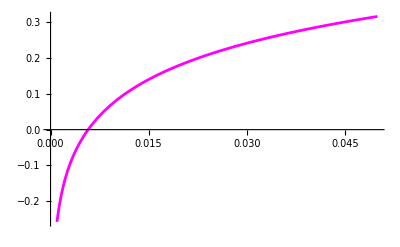

```mathematica
Plot[ {1.16*LasymNf3[ x^2 ],1.16*LasymNf3Test[ x^2 ]}, {x, 0, 0.05}, PlotStyle->{Magenta,{Black, Dashed}}]
```

Fit of the gluon:

```mathematica
gluonNf2 = Compile[ {{x, _Real}}, Module[ { mu2 = 2^2, Ca = 3,  Nf = 2, TR = 1/2, β0, ω, Aq, Padq, Padmu , γ, eta1 = 10.1, eta2 = 0.895, b0 = - 0.0998, b1 = - 1.67, b2 = 0.684, b3 = 0.321, kappa = 71.8, d = 0.112 }, 

β0 = 11*Ca/3 - 4/3*TR*Nf;

γ = ( 13*Ca/6 - 4/3*TR*Nf )/β0;

ω = 0.421; (*Corresponding to Subscript[Λ, T]=609.5 MeV and μ = 3.61, recalling Subscript[Λ, T]^2= μ^2*Exp[ - 1/ω ] *)

 (* ω = as/( 4*π )*( 11*Ca/3 - 4/3*TR*Nf ); One-loop *)


Padq=(b0+x/b1 )/(1 +x/b2+(x/b3)^2 ); 

Padmu=(b0+mu2/b1)/(1 +mu2/b2+(x/b3)^2);

Aq = ( 1 + ω*Log[ ( x + eta1/( 1 + x/eta2 ) )/( mu2 + eta1/( 1 + x/eta2 ) ) ] ); 

1/( x*( d/( 1 + x/kappa )*Log[ x/mu2 ] + Aq^γ )  + Padq - Padmu  )

],CompilationOptions->{"InlineCompiledFunctions"->True, "InlineExternalDefinitions"->True },RuntimeOptions->"Speed", CompilationTarget->"C"];
```

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

Fit of the Z:

```mathematica
ZANf2= Compile[ {{x, _Real}}, 1/(x*gluonNf2[x]) 

,CompilationOptions->{"InlineCompiledFunctions"->True, "InlineExternalDefinitions"->True },RuntimeOptions->"Speed"];
```

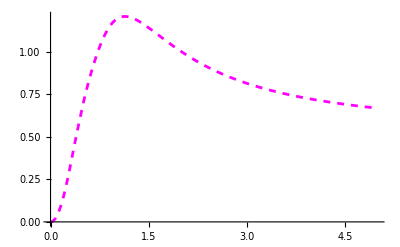

```mathematica
Plot[ {1/ZANf2[ x^2 ]}, {x, 0, 5}, PlotStyle->{Dashed,Magenta}]
```

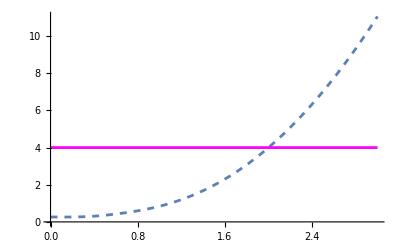

```mathematica
Plot[ {1/gluonNf2[x^2],4}, {x, 0, 3}, PlotStyle->{Dashed,Magenta}]
```

Quark propagator:

```mathematica
Quark0[q_]:=(γ.q+mq 𝟙)/(q.q-mq^2)
Quark[q_]:=(QA[δ q.q]*γ.q+DiracMatrix[]*QB[δ q.q])/(q.q*QA[δ q.q]^2-QB[δ q.q]^2)
```

Fit of the mass:

```mathematica
QMassNf2 = Compile[ {{x, _Real}}, Module[{mq = 0.0062, Aq, Nf = 2, γ, Λ = 0.6095, m0 = 0.345, kappa2 = 0.520, δ = 1.29, eta1 = 1.31, eta2 = 13.0  },  

γ = 12/( 33 - 2 Nf ); Aq = Log[  ( x + eta1/( 1 + x/eta2 ) )/( Λ^2)  ] ; m0/( 1 + ( x/kappa2 )^δ) + mq/( 1/2*Aq )^γ ]

,CompilationOptions->{"InlineCompiledFunctions"->True, "InlineExternalDefinitions"->True },RuntimeOptions->"Speed", CompilationTarget->"C"];
```

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

Fit of the quark wave function:

```mathematica
QZNf2mon = Compile[ {{x, _Real}}, Module[  { mu2 = 2^2, Padq, Padmu, b0 = 0.360, b1 = 0.642, b2 = 0.175, b3 = 0.462, kappa2 = 0.930 },

Padq = ( b0 + x/b1 + ( x/kappa2)^2 )/( 1 + x/b2 + (x/b3)^2 );

Padmu = ( b0 + mu2/b1 + ( mu2/kappa2)^2 )/( 1 + mu2/b2 + (mu2/b3)^2 ); Padmu/Padq]

,CompilationOptions->{"InlineCompiledFunctions"->True, "InlineExternalDefinitions"->True },RuntimeOptions->"Speed", CompilationTarget->"C"];
```

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

Quark A:

```mathematica
QANf2 = Compile[ {{x, _Real}}, 1/QZNf2mon[ x ]

,CompilationOptions->{"InlineCompiledFunctions"->True, "InlineExternalDefinitions"->True },RuntimeOptions->"Speed", CompilationTarget->"C"];
```

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

Quark B:

```mathematica
QBNf2 = Compile[ {{x, _Real}}, QMassNf2[ x ]*QANf2[ x ]

,CompilationOptions->{"InlineCompiledFunctions"->True, "InlineExternalDefinitions"->True },RuntimeOptions->"Speed", CompilationTarget->"C"];
```

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

```mathematica
QMassNf2[ 0]
```

0.352506

```mathematica
QBNf2[4]
```

0.0287166

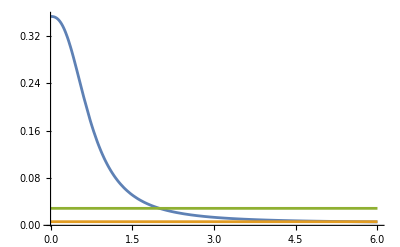

```mathematica
Plot[{QMassNf2[p^2],0.0062,QMassNf2[2^2]},{p,0,6},PlotRange->All]
```

```mathematica
6.2/1000
```

0.0062

```mathematica
QMassNf2[6^2]
```

0.0058512

```mathematica
QANf2[2^2]
```

1.

### Basis:

General kinematics:

-Graphics-

```mathematica
Τp1[μ_,q_,p2_,p1_]:=Contract[TP[q,μ,ν] DiracMatrix[Subscript[γ, ν]]];
Τp2[μ_,q_,p2_,p1_]:=Contract[TP[q,μ,ν] Subscript[(p2+p1), ν]*DiracMatrix[]];
Τp3[μ_,q_,p2_,p1_]:= Contract[TP[q,μ,ν]DiracMatrix[(γ.p2+γ.p1),Subscript[γ, ν]]];
Τp4[μ_,q_,p2_,p1_]:=-Contract[TP[q,μ,ν]DiracMatrix[(γ.p2-γ.p1),Subscript[γ, ν]]];
Τp5[μ_,q_,p2_,p1_]:=Contract[TP[q,μ,ν]DiracMatrix[γ.(p1-p2)]*Subscript[(p2+p1), ν]];
Τp6[μ_,q_,p2_,p1_]:=Contract[TP[q,μ,ν]DiracMatrix[γ.(p2+p1)]*Subscript[(p2+p1), ν]];
Τp7[μ_,q_,p2_,p1_]:=-Contract[DiracMatrix[TP[q,μ,ν](DiracMatrix[γ.p1,γ.p2]-DiracMatrix[γ.p2,γ.p1]),Subscript[γ, ν]]/2];
Τp8[μ_,q_,p2_,p1_]:=-Contract[TP[q,μ,ν](DiracMatrix[γ.p1,γ.p2]-DiracMatrix[γ.p2,γ.p1])Subscript[(p2+p1), ν]/2];
```

### Diagrams:

-Graphics--Graphics-

Diagrams projected

```mathematica
A[μ_,q_,p2_,p1_,k_]:=Contract[-ⅈ*TP[q,μ,α]*coupA*Gluon[k,ρ,ν]DiracMatrix[ΓQqq[ρ,-k,p1+k,-p1],Quark[p1+k],ΓQqq[α,q,p2+k,-p1-k],Quark[p2+k],ΓQqq[ν,k,p2,-p2-k]]*dk]
B[μ_,q_,p2_,p1_,k_]:=Contract[ⅈ*coupB*TP[q,μ,α]* Γ0Q3[α,β,σ,q,k-p1,p2-k] L[δ*(q.q+(k-p1).(k-p1)+(p2-k).(p2-k))/2] Gluon[p1-k,β,ρ]Gluon[p2-k,ν,σ]DiracMatrix[ΓQqq[ρ,p1-k,k,-p1],Quark[k],ΓQqq[ν,k-p2,p2,-k]]* dk]
```

Diagrams projected without coups : Kernels

```mathematica
Awc[μ_,q_,p2_,p1_,k_]:=Contract[-ⅈ*TP[q,μ,α]*Gluon[k,ρ,ν]DiracMatrix[ΓQqqwl[ρ,-k,p1+k,-p1],Quark[p1+k],ΓQqqwl[α,q,p2+k,-p1-k],Quark[p2+k],ΓQqqwl[ν,k,p2,-p2-k]]*dk]
Bwc[μ_,q_,p2_,p1_,k_]:=Contract[ⅈ*TP[q,μ,α]* Γ0Q3[α,β,σ,q,k-p1,p2-k] L[δ*(q.q+(k-p1).(k-p1)+(p2-k).(p2-k))/2] Gluon[p1-k,β,ρ]Gluon[p2-k,ν,σ]DiracMatrix[ΓQqqwl[ρ,p1-k,k,-p1],Quark[k],ΓQqqwl[ν,k-p2,p2,-k]]* dk]
```

### Contractions:

Equation (3.31)

Contractions in general kinematics:

```mathematica
C1A=FermionLineExpand[Contract[Spur[DiracMatrix[Τp1[μ,q,p2,p1],A[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C1B=FermionLineExpand[Contract[Spur[DiracMatrix[Τp1[μ,q,p2,p1],B[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C2A=FermionLineExpand[Contract[Spur[DiracMatrix[Τp2[μ,q,p2,p1],A[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C2B=FermionLineExpand[Contract[Spur[DiracMatrix[Τp2[μ,q,p2,p1],B[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C3A=FermionLineExpand[Contract[Spur[DiracMatrix[Τp3[μ,q,p2,p1],A[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C3B=FermionLineExpand[Contract[Spur[DiracMatrix[Τp3[μ,q,p2,p1],B[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C4A=FermionLineExpand[Contract[Spur[DiracMatrix[Τp4[μ,q,p2,p1],A[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C4B=FermionLineExpand[Contract[Spur[DiracMatrix[Τp4[μ,q,p2,p1],B[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C5A=FermionLineExpand[Contract[Spur[DiracMatrix[Τp5[μ,q,p2,p1],A[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C5B=FermionLineExpand[Contract[Spur[DiracMatrix[Τp5[μ,q,p2,p1],B[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C6A=FermionLineExpand[Contract[Spur[DiracMatrix[Τp6[μ,q,p2,p1],A[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C6B=FermionLineExpand[Contract[Spur[DiracMatrix[Τp6[μ,q,p2,p1],B[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C7A=FermionLineExpand[Contract[Spur[DiracMatrix[Τp7[μ,q,p2,p1],A[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C7B=FermionLineExpand[Contract[Spur[DiracMatrix[Τp7[μ,q,p2,p1],B[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C8A=FermionLineExpand[Contract[Spur[DiracMatrix[Τp8[μ,q,p2,p1],A[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C8B=FermionLineExpand[Contract[Spur[DiracMatrix[Τp8[μ,q,p2,p1],B[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

Contractions without coups in general kinematics:

```mathematica
C1Awc=FermionLineExpand[Contract[Spur[DiracMatrix[Τp1[μ,q,p2,p1],Awc[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C1Bwc=FermionLineExpand[Contract[Spur[DiracMatrix[Τp1[μ,q,p2,p1],Bwc[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C2Awc=FermionLineExpand[Contract[Spur[DiracMatrix[Τp2[μ,q,p2,p1],Awc[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C2Bwc=FermionLineExpand[Contract[Spur[DiracMatrix[Τp2[μ,q,p2,p1],Bwc[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C3Awc=FermionLineExpand[Contract[Spur[DiracMatrix[Τp3[μ,q,p2,p1],Awc[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C3Bwc=FermionLineExpand[Contract[Spur[DiracMatrix[Τp3[μ,q,p2,p1],Bwc[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C4Awc=FermionLineExpand[Contract[Spur[DiracMatrix[Τp4[μ,q,p2,p1],Awc[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C4Bwc=FermionLineExpand[Contract[Spur[DiracMatrix[Τp4[μ,q,p2,p1],Bwc[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C5Awc=FermionLineExpand[Contract[Spur[DiracMatrix[Τp5[μ,q,p2,p1],Awc[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C5Bwc=FermionLineExpand[Contract[Spur[DiracMatrix[Τp5[μ,q,p2,p1],Bwc[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C6Awc=FermionLineExpand[Contract[Spur[DiracMatrix[Τp6[μ,q,p2,p1],Awc[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C6Bwc=FermionLineExpand[Contract[Spur[DiracMatrix[Τp6[μ,q,p2,p1],Bwc[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C7Awc=FermionLineExpand[Contract[Spur[DiracMatrix[Τp7[μ,q,p2,p1],Awc[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C7Bwc=FermionLineExpand[Contract[Spur[DiracMatrix[Τp7[μ,q,p2,p1],Bwc[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C8Awc=FermionLineExpand[Contract[Spur[DiracMatrix[Τp8[μ,q,p2,p1],Awc[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

```mathematica
C8Bwc=FermionLineExpand[Contract[Spur[DiracMatrix[Τp8[μ,q,p2,p1],Bwc[μ,q,p2,p1,k]]]]]/.𝒹->4//Simplify;
```

## Kernel expressions for A and B

## K1

### K1A

-Graphics-

```mathematica
(*Ruleλ={λ1[q_,r_,p_]->λ1[δ*(p.p+r.r+q.q)/2]}*)
```

```mathematica
K1Aeuc=(4h[p1,p2]*C1Awc+(p1.p1-p2.p2)C5Awc-q.q*C6Awc)/(32h[p1,p2])/.q->p1-p2/.RuleKernelAB/.Ruleλ/.RuleAng/.RuleEuc//Simplify
```

-((Csc[θ]^2 ((-2+2 Cos[θ]^2+Cos[ϕ]^2-2 Cos[θ] Cos[ϕ] Cos[ϕ1]+Cos[ϕ1]^2) QB[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]-1/4 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]] (-2 p1 p2 Cos[θ]^3+2 Cos[θ]^2 (-p2 Cos[ϕ] (k-4 p1 Cos[ϕ1])+k (k-p1 Cos[ϕ1]))+k (k+k Cos[2 θ]+4 k Cos[ϕ]^2+2 k Cos[2 ϕ]+2 p1 Cos[ϕ1]+4 k Cos[ϕ1]^2+2 k Cos[2 ϕ1]+2 p1 Cos[ϕ1] Sin[θ]^2+2 p2 Cos[ϕ] (1+Sin[θ]^2))+Cos[θ] (p1 p2-3 p1 p2 Cos[2 θ]-2 p1 p2 Cos[2 ϕ]-16 k^2 Cos[ϕ] Cos[ϕ1]-2 p1 p2 Cos[ϕ1]^2+2 p1 p2 Sin[ϕ1]^2))))/(((k^2+p2^2+2 k p2 Cos[ϕ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2+QB[k^2+p2^2+2 k p2 Cos[ϕ]]^2) ((k^2+p1^2+2 k p1 Cos[ϕ1]) QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2+QB[k^2+p1^2+2 k p1 Cos[ϕ1]]^2)))

### K1B

-Graphics-

```mathematica
(*Ruleλ={λ1[q_,r_,p_]->λ1[δ*(p.p+r.r+q.q)/2]}*)
```

```mathematica
K1Beuc=(4h[p1,p2]*C1Bwc+(p1.p1-p2.p2)C5Bwc-q.q*C6Bwc)/(32h[p1,p2])/.q->p1-p2/.RuleKernelAB/.Ruleλ/.RuleAng/.RuleEuc//Simplify
```

-((k (-2 k p1^2 p2^2 Cos[θ]^4-2 k^2 p2 Cos[ϕ]^3 (5 k^2+4 p1^2-8 k p1 Cos[ϕ1])+2 k^2 Cos[ϕ]^2 (k (3 k^2+2 p1^2+4 p2^2)-p1 (5 k^2+4 p2^2) Cos[ϕ1])+2 (-3 k^5-6 k p1^2 p2^2-4 k^3 (p1^2+p2^2)+p1 (5 k^4+10 k^2 p2^2+2 p1^2 p2^2) Cos[ϕ1]+k^3 (3 k^2+4 p1^2+2 p2^2) Cos[ϕ1]^2-k^2 p1 (5 k^2+4 p2^2) Cos[ϕ1]^3)+2 p1 p2 Cos[θ]^3 (-2 k (2 k^2+p1^2+p2^2)+p1 (7 k^2+2 p2^2) Cos[ϕ1]+p2 Cos[ϕ] (7 k^2+2 p1^2-6 k p1 Cos[ϕ1]))-2 Cos[θ] (-k^2 p1 p2^2 Cos[ϕ]^3+k^2 p2 Cos[ϕ]^2 Cos[ϕ1] (-10 k^2-9 p1^2+16 k p1 Cos[ϕ1])+Cos[ϕ] (p1 (7 k^2+2 p1^2) p2^2+(6 k^5-4 k p1^2 p2^2+4 k^3 (p1^2+p2^2)) Cos[ϕ1]-k^2 p1 (10 k^2+9 p2^2) Cos[ϕ1]^2)-p1 p2 (2 k (2 k^2+p1^2+p2^2)-p1 (7 k^2+2 p2^2) Cos[ϕ1]+k^2 p1 Cos[ϕ1]^3))+2 Cos[θ]^2 (3 k^5+4 k^3 p1^2+4 k^3 p2^2+7 k p1^2 p2^2-p1 (5 k^4+10 k^2 p2^2+2 p1^2 p2^2) Cos[ϕ1]-k p1^2 (2 k^2-p2^2) Cos[ϕ1]^2-k p2^2 Cos[ϕ]^2 (2 k^2-p1^2+2 k p1 Cos[ϕ1])+p2 Cos[ϕ] (-5 k^4-11 k^2 p1^2-2 p1^2 p2^2+2 k p1 (6 k^2+p1^2+p2^2) Cos[ϕ1]-k^2 p1^2 Cos[2 ϕ1]))-p2 Cos[ϕ] (-5 k^4-16 k^2 p1^2-4 p1^2 p2^2+4 k p1 (3 k^2+p1^2+p2^2) Cos[ϕ1]+k^2 (5 k^2+4 p1^2) Cos[2 ϕ1]-4 k^3 p1 Cos[3 ϕ1])) Csc[θ]^2 QA[k^2])/(2 (k^2+p2^2-2 k p2 Cos[ϕ]) (k^2+p1^2-2 k p1 Cos[ϕ1]) (k^2 QA[k^2]^2+QB[k^2]^2)))

## K2

### K2A

-Graphics-

```mathematica
K2Aeuc=(1/(32h[p1,p2]) (q.q*C2Awc+q.q*C3Awc+(p2.p2-p1.p1)C4Awc))/.q->p1-p2/.RuleKernelAB/.Ruleλ/.RuleAng/.RuleEuc
```

1/(32 (p1^2 p2^2-p1^2 p2^2 Cos[θ]^2))((12 ((-p1^2+p1 p2 Cos[θ])^2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+k p2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ] QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+k p1 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ1] QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+(p2^2-p1 p2 Cos[θ])^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]+p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]+p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]+k p2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ] QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]+k p1 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ1] QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]+(p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) (QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]])+(-p1^2+p2^2) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]) (QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]])))/((-k^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2-p2^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2-2 k p2 Cos[ϕ] QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2-QB[k^2+p2^2+2 k p2 Cos[ϕ]]^2) (-k^2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2-p1^2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2-2 k p1 Cos[ϕ1] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2-QB[k^2+p1^2+2 k p1 Cos[ϕ1]]^2))+(4 (p1^2-p2^2) (-2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]) (-k p1 Cos[ϕ1] QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+k p2 Cos[ϕ] QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]])+2 (k p2 Cos[ϕ]-k p1 Cos[ϕ1])^2 (-p1^2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]-p2^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]+p1 p2 Cos[θ] (QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]))+2 (k p2 Cos[ϕ]-k p1 Cos[ϕ1]) (k^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) (2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]])-k p1 Cos[ϕ1] (-2 (-p1^2+p1 p2 Cos[θ]) QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+(p2^2-p1 p2 Cos[θ]) (QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]))-k p2 Cos[ϕ] (-2 (p2^2-p1 p2 Cos[θ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]+(-p1^2+p1 p2 Cos[θ]) (QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]])))-k^2 (-2 (-p1^2+p1 p2 Cos[θ])^2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+4 (p2^2-p1 p2 Cos[θ])^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]+2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) (QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]-2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]])+(-p1^2-p2^2+2 p1 p2 Cos[θ]) (-3 p1^2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+3 p2^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]-3 p1 p2 Cos[θ] (-QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]])+k p2 Cos[ϕ] (QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+5 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]])-k p1 Cos[ϕ1] (QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+5 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]])))))/(k^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) (-k^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2-p2^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2-2 k p2 Cos[ϕ] QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2-QB[k^2+p2^2+2 k p2 Cos[ϕ]]^2) (-k^2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2-p1^2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2-2 k p1 Cos[ϕ1] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2-QB[k^2+p1^2+2 k p1 Cos[ϕ1]]^2))+(4 (-2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) (-k p2 Cos[ϕ]-k p1 Cos[ϕ1]) (-k p1 Cos[ϕ1] QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+k p2 Cos[ϕ] QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]])-2 (k p2 Cos[ϕ]-k p1 Cos[ϕ1])^2 (p1^2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]-p2^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]-p1 p2 Cos[θ] (-QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]))-2 (k p2 Cos[ϕ]-k p1 Cos[ϕ1]) (-k^2 (-p1^2+p2^2) (2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]])-k p1 Cos[ϕ1] (2 (-p1^2+p1 p2 Cos[θ]) QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+(p2^2-p1 p2 Cos[θ]) (QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]-QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]))-k p2 Cos[ϕ] (-2 (p2^2-p1 p2 Cos[θ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]+(-p1^2+p1 p2 Cos[θ]) (QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]-QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]])))-k^2 (-2 (-p1^2+p1 p2 Cos[θ])^2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]-4 (p2^2-p1 p2 Cos[θ])^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]-2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) (QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]])+(-p1^2-p2^2+2 p1 p2 Cos[θ]) (-k p2 Cos[ϕ] (QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+5 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]])-k p1 Cos[ϕ1] (QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+5 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]])+3 (-p1^2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]-p2^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]-p1 p2 Cos[θ] (QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]]+QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]))))))/(k^2 (-k^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2-p2^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2-2 k p2 Cos[ϕ] QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2-QB[k^2+p2^2+2 k p2 Cos[ϕ]]^2) (-k^2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2-p1^2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2-2 k p1 Cos[ϕ1] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2-QB[k^2+p1^2+2 k p1 Cos[ϕ1]]^2)))

### K2B

-Graphics-

```mathematica
K2Beuc=(1/(32h[p1,p2]) (q.q*C2Bwc+q.q*C3Bwc+(p2.p2-p1.p1)C4Bwc))/.q->p1-p2/.RuleKernelAB/.Ruleλ/.RuleAng/.RuleEuc
```

1/(32 (p1^2 p2^2-p1^2 p2^2 Cos[θ]^2))((4 (-2 p1^2 p2^2 (p2^2-p1 p2 Cos[θ])^2-p1^3 p2 Cos[θ] (p2^2-p1 p2 Cos[θ])^2-4 p1^2 p2^2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])-p1^3 p2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])-p1 p2^3 Cos[θ] (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])-2 p1^2 p2^2 (-p1^2+p1 p2 Cos[θ])^2-p1 p2^3 Cos[θ] (-p1^2+p1 p2 Cos[θ])^2-2 p1^4 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-2 p1^2 p2^4 (-p1^2-p2^2+2 p1 p2 Cos[θ])-6 p1^3 p2^3 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])-p1^4 p2^2 Cos[θ]^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-p1^2 p2^4 Cos[θ]^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-p1^3 p2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-p1^2 p2^2 Cos[θ]^2 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+p1 p2^3 Cos[θ] (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+p1^2 p2^2 Cos[θ]^2 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+5 k p1^2 p2 (p2^2-p1 p2 Cos[θ])^2 Cos[ϕ]+9 k p1^2 p2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) Cos[ϕ]+k p2^3 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) Cos[ϕ]+2 k p1 p2^2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) Cos[ϕ]+4 k p1^2 p2 (-p1^2+p1 p2 Cos[θ])^2 Cos[ϕ]+k p2^3 (-p1^2+p1 p2 Cos[θ])^2 Cos[ϕ]+2 k p1 p2^2 Cos[θ] (-p1^2+p1 p2 Cos[θ])^2 Cos[ϕ]+4 k p1^4 p2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+10 k p1^2 p2^3 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+12 k p1^3 p2^2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+2 k p1 p2^4 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+2 k p1^2 p2^3 Cos[θ]^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+k p1^2 p2 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+2 k p1 p2^2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]-k p2^3 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]-2 k p1 p2^2 Cos[θ] (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]-2 k^2 p2^2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) Cos[ϕ]^2-2 k^2 p2^2 (-p1^2+p1 p2 Cos[θ])^2 Cos[ϕ]^2-11 k^2 p1^2 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2-k^2 p2^4 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2-4 k^2 p1 p2^3 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2-k^2 p2^2 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2+k^2 p2^2 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2+2 k^3 p2^3 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^3+2 k^3 p1^3 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ1]^3+4 p1^2 p2^2 (p2^2-p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+p1^3 p2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+p1 p2^3 Cos[θ] (p2^2-p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+4 p1^2 p2^2 (-p1^2+p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+p1^3 p2 Cos[θ] (-p1^2+p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+p1 p2^3 Cos[θ] (-p1^2+p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+p1^3 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-p1 p2^3 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-9 k p1^2 p2 (p2^2-p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-k p2^3 (p2^2-p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-2 k p1 p2^2 Cos[θ] (p2^2-p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-9 k p1^2 p2 (-p1^2+p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-k p2^3 (-p1^2+p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-2 k p1 p2^2 Cos[θ] (-p1^2+p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-k p1^2 p2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+k p2^3 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+2 k^2 p2^2 (p2^2-p1 p2 Cos[θ]) Cos[ϕ]^2 (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+2 k^2 p2^2 (-p1^2+p1 p2 Cos[θ]) Cos[ϕ]^2 (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+k^2 p1^2 Cos[ϕ1]^2 (-2 (p2^2-p1 p2 Cos[θ])^2-p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-11 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-4 p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])-(p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+(-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ]-2 (p2^2-p1 p2 Cos[θ]))+22 k p2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+2 (-p1^2+p2^2) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]))+3 k^4 (-(p2^2-p1 p2 Cos[θ])^2-2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])-(-p1^2+p1 p2 Cos[θ])^2-p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-2 p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])+2 k p2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+2 k p1 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ1]+2 (-p1^2+p2^2) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]))+k p1 Cos[ϕ1] (p1^2 (p2^2-p1 p2 Cos[θ])^2+4 p2^2 (p2^2-p1 p2 Cos[θ])^2+2 p1 p2 Cos[θ] (p2^2-p1 p2 Cos[θ])^2+p1^2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])+9 p2^2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])+2 p1 p2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])+5 p2^2 (-p1^2+p1 p2 Cos[θ])^2+10 p1^2 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+4 p2^4 (-p1^2-p2^2+2 p1 p2 Cos[θ])+2 p1^3 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])+12 p1 p2^3 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])+2 p1^2 p2^2 Cos[θ]^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+p1^2 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+2 p1 p2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-p2^2 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-2 p1 p2 Cos[θ] (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+22 k^2 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2+(-2 p1 p2 (-p1^2+p2^2) Cos[θ]-p1^2 (-2 p1^2+2 p1 p2 Cos[θ])-p2^2 (p1^2+p2^2-2 p1 p2 Cos[θ]+9 (p2^2-p1 p2 Cos[θ])+9 (-p1^2+p1 p2 Cos[θ]))) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+2 k p2 Cos[ϕ] (-5 (p2^2-p1 p2 Cos[θ])^2-5 (-p1^2+p1 p2 Cos[θ])^2-10 p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-10 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-12 p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])-(p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+(-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ]-10 (p2^2-p1 p2 Cos[θ]))+10 (-p1^2+p2^2) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])))-k^2 (3 p1^2 (p2^2-p1 p2 Cos[θ])^2+2 p2^2 (p2^2-p1 p2 Cos[θ])^2+p1 p2 Cos[θ] (p2^2-p1 p2 Cos[θ])^2+5 p1^2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])+5 p2^2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])+2 p1 p2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])+2 p1^2 (-p1^2+p1 p2 Cos[θ])^2+3 p2^2 (-p1^2+p1 p2 Cos[θ])^2+p1 p2 Cos[θ] (-p1^2+p1 p2 Cos[θ])^2+2 p1^4 (-p1^2-p2^2+2 p1 p2 Cos[θ])+6 p1^2 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+2 p2^4 (-p1^2-p2^2+2 p1 p2 Cos[θ])+6 p1^3 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])+6 p1 p2^3 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])+2 p1^2 p2^2 Cos[θ]^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+p1^2 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+p1 p2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-p2^2 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-p1 p2 Cos[θ] (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+12 k^2 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2+12 k^2 p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ1]^2-5 p1^2 (p2^2-p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-5 p2^2 (p2^2-p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-2 p1 p2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-5 p1^2 (-p1^2+p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-5 p2^2 (-p1^2+p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-2 p1 p2 Cos[θ] (-p1^2+p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-k p1 Cos[ϕ1] (7 (p2^2-p1 p2 Cos[θ])^2+5 (-p1^2+p1 p2 Cos[θ])^2+10 p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+12 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+14 p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])+(p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+(-p1^2+p1 p2 Cos[θ]) (p1^2+p2^2-2 p1 p2 Cos[θ]+12 (p2^2-p1 p2 Cos[θ]))-24 k p2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]-12 (-p1^2+p2^2) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]))+k p2 Cos[ϕ] (-5 (p2^2-p1 p2 Cos[θ])^2-7 (-p1^2+p1 p2 Cos[θ])^2-12 p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-10 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-14 p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])-(p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+(-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ]-12 (p2^2-p1 p2 Cos[θ]))+12 (-p1^2+p2^2) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])))) QB[k^2])/((-k^2-p2^2+2 k p2 Cos[ϕ]) (-k^2-p1^2+2 k p1 Cos[ϕ1]) (-k^2 QA[k^2]^2-QB[k^2]^2))-(4 (p1^2 p2^2 (p2^2-p1 p2 Cos[θ])^2+4 p1^2 p2^2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])+2 p1 p2^3 Cos[θ] (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])+3 p1^2 p2^2 (-p1^2+p1 p2 Cos[θ])^2+2 p1 p2^3 Cos[θ] (-p1^2+p1 p2 Cos[θ])^2+4 p1^2 p2^4 (-p1^2-p2^2+2 p1 p2 Cos[θ])+6 p1^3 p2^3 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])+3 p1^4 p2^2 Cos[θ]^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-p1^2 p2^4 Cos[θ]^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+3 p1^2 p2^2 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-p1^3 p2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+3 p1^2 p2^2 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-3 p1 p2^3 Cos[θ] (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-2 p1^2 p2^2 Cos[θ]^2 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-2 k p1^2 p2 (p2^2-p1 p2 Cos[θ])^2 Cos[ϕ]-8 k p1^2 p2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) Cos[ϕ]-2 k p2^3 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) Cos[ϕ]-4 k p1 p2^2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) Cos[ϕ]-6 k p1^2 p2 (-p1^2+p1 p2 Cos[θ])^2 Cos[ϕ]-2 k p2^3 (-p1^2+p1 p2 Cos[θ])^2 Cos[ϕ]-4 k p1 p2^2 Cos[θ] (-p1^2+p1 p2 Cos[θ])^2 Cos[ϕ]-14 k p1^2 p2^3 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]-12 k p1^3 p2^2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+2 k p1 p2^4 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+2 k p1^2 p2^3 Cos[θ]^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]-7 k p1^2 p2 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]-6 k p1^2 p2 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+3 k p2^3 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+6 k p1 p2^2 Cos[θ] (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+4 k^2 p2^2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) Cos[ϕ]^2+4 k^2 p2^2 (-p1^2+p1 p2 Cos[θ])^2 Cos[ϕ]^2+9 k^2 p1^2 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2-k^2 p2^4 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2-4 k^2 p1 p2^3 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2-4 k^2 p2^2 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2+2 k^3 p2^3 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^3-6 k^3 p1^3 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ1]^3-4 p1^2 p2^2 (p2^2-p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-2 p1 p2^3 Cos[θ] (p2^2-p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-4 p1^2 p2^2 (-p1^2+p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-2 p1 p2^3 Cos[θ] (-p1^2+p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+2 p1^2 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+p1^3 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+3 p1 p2^3 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+2 p1^2 p2^2 Cos[θ]^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+8 k p1^2 p2 (p2^2-p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+2 k p2^3 (p2^2-p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+4 k p1 p2^2 Cos[θ] (p2^2-p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+8 k p1^2 p2 (-p1^2+p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+2 k p2^3 (-p1^2+p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+4 k p1 p2^2 Cos[θ] (-p1^2+p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-3 k p1^2 p2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-3 k p2^3 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-6 k p1 p2^2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-4 k^2 p2^2 (p2^2-p1 p2 Cos[θ]) Cos[ϕ]^2 (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-4 k^2 p2^2 (-p1^2+p1 p2 Cos[θ]) Cos[ϕ]^2 (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+4 k^2 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2 (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+k^2 p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ1]^2 (3 p1^2+13 p2^2+12 p1 p2 Cos[θ]-2 (p2^2-p1 p2 Cos[θ])-2 (-p1^2+p1 p2 Cos[θ])-26 k p2 Cos[ϕ]+4 (k p2 Cos[ϕ]-k p1 Cos[ϕ1]))+k^4 ((p2^2-p1 p2 Cos[θ])^2+5 (-p1^2+p1 p2 Cos[θ])^2-p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+7 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+6 p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])+4 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+(-p1^2+p1 p2 Cos[θ]) (6 (p2^2-p1 p2 Cos[θ])+4 (-p1^2-p2^2+2 p1 p2 Cos[θ]))-6 k p2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]-6 k p1 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ1]-6 (-p1^2+p2^2) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]))-k p1 Cos[ϕ1] (2 p2^2 (p2^2-p1 p2 Cos[θ])^2+10 p2^2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])+8 p2^2 (-p1^2+p1 p2 Cos[θ])^2+6 p1^2 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+8 p2^4 (-p1^2-p2^2+2 p1 p2 Cos[θ])+6 p1^3 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])+12 p1 p2^3 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])+6 p1^2 p2^2 Cos[θ]^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-p1^2 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+6 p2^2 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-2 p1 p2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+5 p2^2 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-4 p1 p2 Cos[θ] (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+18 k^2 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2+(-10 p2^2 (-p1^2+p1 p2 Cos[θ])-(-p1^2-6 p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-5 p2^2 (p1^2+p2^2-2 p1 p2 Cos[θ]+2 (p2^2-p1 p2 Cos[θ]))) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+2 k p2 Cos[ϕ] (-2 (p2^2-p1 p2 Cos[θ])^2-8 (-p1^2+p1 p2 Cos[θ])^2-6 p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-14 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-12 p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])-7 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-5 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ]+2 (p2^2-p1 p2 Cos[θ]))+2 (5 (p2^2-p1 p2 Cos[θ])+5 (-p1^2+p1 p2 Cos[θ])-2 (-p1^2-p2^2+2 p1 p2 Cos[θ])) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])))-k^2 (-p1^2 (p2^2-p1 p2 Cos[θ])^2-p2^2 (p2^2-p1 p2 Cos[θ])^2-4 p1^2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])-6 p2^2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])-2 p1 p2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])-3 p1^2 (-p1^2+p1 p2 Cos[θ])^2-5 p2^2 (-p1^2+p1 p2 Cos[θ])^2-2 p1 p2 Cos[θ] (-p1^2+p1 p2 Cos[θ])^2-6 p1^2 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-4 p2^4 (-p1^2-p2^2+2 p1 p2 Cos[θ])-6 p1^3 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])-6 p1 p2^3 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])-2 p1^2 p2^2 Cos[θ]^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-4 p1^2 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-3 p2^2 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+p1 p2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-3 p1^2 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-2 p2^2 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+3 p1 p2 Cos[θ] (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-8 k^2 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2-16 k^2 p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ1]^2+4 p1^2 (p2^2-p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+6 p2^2 (p2^2-p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+2 p1 p2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+4 p1^2 (-p1^2+p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+6 p2^2 (-p1^2+p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+2 p1 p2 Cos[θ] (-p1^2+p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-3 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-4 p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-k p1 Cos[ϕ1] (-2 (p2^2-p1 p2 Cos[θ])^2-8 (-p1^2+p1 p2 Cos[θ])^2-6 p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-20 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-18 p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])-7 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-5 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ]+2 (p2^2-p1 p2 Cos[θ]))+24 k p2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+2 (5 (p2^2-p1 p2 Cos[θ])+5 (-p1^2+p1 p2 Cos[θ])-2 (-p1^2-p2^2+2 p1 p2 Cos[θ])) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]))-k p2 Cos[ϕ] (-2 (p2^2-p1 p2 Cos[θ])^2-12 (-p1^2+p1 p2 Cos[θ])^2-4 p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-14 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-10 p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])-7 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-(-p1^2+p1 p2 Cos[θ]) (14 (p2^2-p1 p2 Cos[θ])+5 (-p1^2-p2^2+2 p1 p2 Cos[θ]))+2 (7 (p2^2-p1 p2 Cos[θ])+7 (-p1^2+p1 p2 Cos[θ])-2 (-p1^2-p2^2+2 p1 p2 Cos[θ])) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])))) QB[k^2])/((-k^2-p2^2+2 k p2 Cos[ϕ]) (-k^2-p1^2+2 k p1 Cos[ϕ1]) (-k^2 QA[k^2]^2-QB[k^2]^2))+(4 (p1^2-p2^2) (p1^2 p2^2 (p2^2-p1 p2 Cos[θ])^2+2 p1^2 p2^2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])+2 p1 p2^3 Cos[θ] (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])-3 p1^2 p2^2 (-p1^2+p1 p2 Cos[θ])^2-2 p1 p2^3 Cos[θ] (-p1^2+p1 p2 Cos[θ])^2+4 p1^2 p2^4 (-p1^2-p2^2+2 p1 p2 Cos[θ])-3 p1^4 p2^2 Cos[θ]^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-p1^2 p2^4 Cos[θ]^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+3 p1^2 p2^2 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+p1^3 p2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-3 p1^2 p2^2 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-3 p1 p2^3 Cos[θ] (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+2 p1^2 p2^2 Cos[θ]^2 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-2 k p1^2 p2 (p2^2-p1 p2 Cos[θ])^2 Cos[ϕ]-4 k p1^2 p2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) Cos[ϕ]-2 k p2^3 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) Cos[ϕ]-4 k p1 p2^2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) Cos[ϕ]+6 k p1^2 p2 (-p1^2+p1 p2 Cos[θ])^2 Cos[ϕ]+2 k p2^3 (-p1^2+p1 p2 Cos[θ])^2 Cos[ϕ]+4 k p1 p2^2 Cos[θ] (-p1^2+p1 p2 Cos[θ])^2 Cos[ϕ]-16 k p1^2 p2^3 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+6 k p1^3 p2^2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+2 k p1 p2^4 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+2 k p1^2 p2^3 Cos[θ]^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]-7 k p1^2 p2 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+6 k p1^2 p2 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+3 k p2^3 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+2 k p1 p2^2 Cos[θ] (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+4 k^2 p2^2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) Cos[ϕ]^2-4 k^2 p2^2 (-p1^2+p1 p2 Cos[θ])^2 Cos[ϕ]^2+13 k^2 p1^2 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2-k^2 p2^4 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2-4 k^2 p1 p2^3 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2-4 k^2 p2^2 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2+2 k^3 p2^3 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^3+6 k^3 p1^3 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ1]^3-4 p1^2 p2^2 (p2^2-p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-2 p1 p2^3 Cos[θ] (p2^2-p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+4 p1^2 p2^2 (-p1^2+p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+2 p1 p2^3 Cos[θ] (-p1^2+p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-p1^3 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+3 p1 p2^3 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-2 p1^2 p2^2 Cos[θ]^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+8 k p1^2 p2 (p2^2-p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+2 k p2^3 (p2^2-p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+4 k p1 p2^2 Cos[θ] (p2^2-p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-8 k p1^2 p2 (-p1^2+p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-2 k p2^3 (-p1^2+p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-4 k p1 p2^2 Cos[θ] (-p1^2+p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+k p1^2 p2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-3 k p2^3 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-2 k p1 p2^2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ] (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-4 k^2 p2^2 (p2^2-p1 p2 Cos[θ]) Cos[ϕ]^2 (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+4 k^2 p2^2 (-p1^2+p1 p2 Cos[θ]) Cos[ϕ]^2 (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+4 k^2 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2 (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+k^2 p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ1]^2 (-3 p1^2-p2^2-12 p1 p2 Cos[θ]+2 (p2^2-p1 p2 Cos[θ])+2 (-p1^2+p1 p2 Cos[θ])+14 k p2 Cos[ϕ]-4 (k p2 Cos[ϕ]-k p1 Cos[ϕ1]))+k^4 ((p2^2-p1 p2 Cos[θ])^2+4 (p1^2+2 p2^2-3 p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])-5 (-p1^2+p1 p2 Cos[θ])^2+p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+7 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-8 p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])+4 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-6 k p2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+6 k p1 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ1]+6 (-p1^2-p2^2+2 p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]))-k p1 Cos[ϕ1] (2 p2^2 (p2^2-p1 p2 Cos[θ])^2+6 p2^2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])-8 p2^2 (-p1^2+p1 p2 Cos[θ])^2+8 p2^4 (-p1^2-p2^2+2 p1 p2 Cos[θ])-6 p1^3 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])-2 p1 p2^3 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])-6 p1^2 p2^2 Cos[θ]^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+p1^2 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+6 p2^2 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+2 p1 p2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-9 p2^2 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+4 p1 p2 Cos[θ] (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+22 k^2 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2+(10 p2^2 (-p1^2+p1 p2 Cos[θ])+(-p1^2-6 p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-p2^2 (10 (p2^2-p1 p2 Cos[θ])-3 (-p1^2-p2^2+2 p1 p2 Cos[θ]))) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-2 k p2 Cos[ϕ] (2 (p2^2-p1 p2 Cos[θ])^2-8 (-p1^2+p1 p2 Cos[θ])^2-3 p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+15 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-8 p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])+7 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+(-p1^2+p1 p2 Cos[θ]) (6 (p2^2-p1 p2 Cos[θ])-7 (-p1^2-p2^2+2 p1 p2 Cos[θ]))+10 (-p1^2-p2^2+2 p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])))-k^2 (-p1^2 (p2^2-p1 p2 Cos[θ])^2-p2^2 (p2^2-p1 p2 Cos[θ])^2-2 p1^2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])-4 p2^2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])-2 p1 p2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])+3 p1^2 (-p1^2+p1 p2 Cos[θ])^2+5 p2^2 (-p1^2+p1 p2 Cos[θ])^2+2 p1 p2 Cos[θ] (-p1^2+p1 p2 Cos[θ])^2-8 p1^2 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-4 p2^4 (-p1^2-p2^2+2 p1 p2 Cos[θ])+6 p1^3 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])+2 p1 p2^3 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])+4 p1^2 p2^2 Cos[θ]^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-4 p1^2 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-3 p2^2 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-p1 p2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+3 p1^2 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+6 p2^2 (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-p1 p2 Cos[θ] (-p1^2+p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])-8 k^2 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2+16 k^2 p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ1]^2+4 p1^2 (p2^2-p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+6 p2^2 (p2^2-p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+2 p1 p2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-4 p1^2 (-p1^2+p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-6 p2^2 (-p1^2+p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-2 p1 p2 Cos[θ] (-p1^2+p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])-3 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+2 p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])+k p1 Cos[ϕ1] (2 (p2^2-p1 p2 Cos[θ])^2-8 (-p1^2+p1 p2 Cos[θ])^2-6 p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+14 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-20 p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])+9 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+(-p1^2+p1 p2 Cos[θ]) (6 (p2^2-p1 p2 Cos[θ])-5 (-p1^2-p2^2+2 p1 p2 Cos[θ]))-8 k p2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+2 (-5 (p2^2-p1 p2 Cos[θ])+5 (-p1^2+p1 p2 Cos[θ])-2 (-p1^2-p2^2+2 p1 p2 Cos[θ])) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]))-k p2 Cos[ϕ] (-2 (p2^2-p1 p2 Cos[θ])^2+12 (-p1^2+p1 p2 Cos[θ])^2-10 p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])-14 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+12 p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])-7 (p2^2-p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])+(-p1^2+p1 p2 Cos[θ]) (-10 (p2^2-p1 p2 Cos[θ])+11 (-p1^2-p2^2+2 p1 p2 Cos[θ]))-2 (-7 (p2^2-p1 p2 Cos[θ])+7 (-p1^2+p1 p2 Cos[θ])+2 (-p1^2-p2^2+2 p1 p2 Cos[θ])) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])))) QB[k^2])/((-p1^2-p2^2+2 p1 p2 Cos[θ]) (-k^2-p2^2+2 k p2 Cos[ϕ]) (-k^2-p1^2+2 k p1 Cos[ϕ1]) (-k^2 QA[k^2]^2-QB[k^2]^2)))

## K3

### K3A

-Graphics-

```mathematica
K3Aeuc=( 1/(32h[p1,p2]) (q.q*C2Awc-q.q*C3Awc+(p1.p1-p2.p2)C4Awc))/.q->p1-p2/.RuleKernelAB/.Ruleλ/.RuleAng/.RuleEuc//Simplify
```

-((Csc[θ]^2 ((p2 (-p1+2 p2 Cos[θ]) Cos[ϕ]^2+Cos[ϕ1] (-k p2+k p1 Cos[θ]+p1 p2 Cos[ϕ1])+Cos[ϕ] (-k p1+k p2 Cos[θ]-2 p2^2 Cos[ϕ1])) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]+1/2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]] (-p1 p2 Cos[2 ϕ]+2 k p2 Cos[ϕ1]-2 k p1 Cos[θ] Cos[ϕ1]+p1 p2 Cos[ϕ1]^2-4 p1^2 Cos[θ] Cos[ϕ1]^2+2 Cos[ϕ] (-k p2 Cos[θ]+p1 (k+2 p1 Cos[ϕ1]))-p1 p2 Sin[ϕ1]^2)))/(2 p1 p2 ((k^2+p2^2+2 k p2 Cos[ϕ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2+QB[k^2+p2^2+2 k p2 Cos[ϕ]]^2) ((k^2+p1^2+2 k p1 Cos[ϕ1]) QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2+QB[k^2+p1^2+2 k p1 Cos[ϕ1]]^2)))

### K3B

-Graphics-

```mathematica
K3Beuc=( 1/(32h[p1,p2]) (q.q*C2Bwc-q.q*C3Bwc+(p1.p1-p2.p2)C4Bwc))/.q->p1-p2/.RuleKernelAB/.Ruleλ/.RuleAng/.RuleEuc//Simplify
```

-(((p1^2-p2^2+2 k p2 Cos[ϕ]-2 k p1 Cos[ϕ1]) Csc[θ]^2 QB[k^2] (p1^2 p2^2 Cos[θ]^3+2 k p1 p2 Cos[θ]^2 (k-2 p2 Cos[ϕ]-2 p1 Cos[ϕ1])+1/2 Cos[θ] (4 k^2 p1^2+4 k^2 p2^2-5 p1^2 p2^2+3 p1^2 p2^2 Cos[2 θ]-8 k (k^2-p1^2) p2 Cos[ϕ]+4 k^2 p2^2 Cos[2 ϕ]+8 k^2 p1 p2 Cos[ϕ-ϕ1]-8 k^3 p1 Cos[ϕ1]+8 k p1 p2^2 Cos[ϕ1]+4 k^2 p1^2 Cos[2 ϕ1]+8 k^2 p1 p2 Cos[ϕ+ϕ1])+2 k (-k p1 p2 Cos[ϕ]^2+2 Cos[ϕ] (-k (p1^2+p2^2) Cos[ϕ1]+p1 (k^2+p2^2 Sin[θ]^2))+p2 (-k p1 Cos[ϕ1]^2+2 Cos[ϕ1] (k^2+p1^2 Sin[θ]^2)+k p1 (-3-Sin[θ]^2+Sin[ϕ]^2+Sin[ϕ1]^2)))))/(4 p1 p2 (k^2+p2^2-2 k p2 Cos[ϕ]) (k^2+p1^2-2 k p1 Cos[ϕ1]) (k^2 QA[k^2]^2+QB[k^2]^2)))

## K4

### K4A

-Graphics-

```mathematica
K4Aeuc=(1/(32h[p1,p2]) ((p2.p2-p1.p1)C2Awc+(p1.p1-p2.p2)C3Awc-(p1+p2).(p1+p2)C4Awc-2*C8Awc))/.q->p1-p2/.RuleKernelAB/.Ruleλ/.RuleAng/.RuleEuc//Simplify
```

-((Csc[θ]^2 ((p2 (p1+2 p2 Cos[θ]) Cos[ϕ]^2+Cos[ϕ] (k p1+k p2 Cos[θ]-2 p2^2 Cos[ϕ1])-Cos[ϕ1] (k p1 Cos[θ]+p2 (k+p1 Cos[ϕ1]))) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]-1/2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]] (p1 p2 Cos[2 ϕ]-2 k p2 Cos[ϕ1]-2 k p1 Cos[θ] Cos[ϕ1]-p1 p2 Cos[ϕ1]^2-4 p1^2 Cos[θ] Cos[ϕ1]^2+2 Cos[ϕ] (k p2 Cos[θ]+p1 (k+2 p1 Cos[ϕ1]))+p1 p2 Sin[ϕ1]^2)))/(2 p1 p2 ((k^2+p2^2+2 k p2 Cos[ϕ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2+QB[k^2+p2^2+2 k p2 Cos[ϕ]]^2) ((k^2+p1^2+2 k p1 Cos[ϕ1]) QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2+QB[k^2+p1^2+2 k p1 Cos[ϕ1]]^2)))

### K4B

-Graphics-

```mathematica
K4Beuc=(1/(32h[p1,p2]) ((p2.p2-p1.p1)C2Bwc+(p1.p1-p2.p2)C3Bwc-(p1+p2).(p1+p2)C4Bwc-2*C8Bwc))/.q->p1-p2/.RuleKernelAB/.Ruleλ/.RuleAng/.RuleEuc//Simplify
```

((-k^3 p1 p2^2 Cos[ϕ]^3+p1^2 p2^2 Cos[θ]^3 (k^2+p1^2+p2^2-2 k p2 Cos[ϕ]-2 k p1 Cos[ϕ1])+k^2 p2 Cos[ϕ]^2 (-p1 (-k^2+p1^2+p2^2)+k (p1^2+2 p2^2) Cos[ϕ1])+p2 (-p1 (3 k^4+2 p1^2 p2^2+3 k^2 (p1^2+p2^2))+k (p1^4+5 p1^2 p2^2+k^2 (6 p1^2+p2^2)) Cos[ϕ1]+k^2 p1 (k^2-p1^2-p2^2) Cos[ϕ1]^2-k^3 p1^2 Cos[ϕ1]^3)+Cos[θ] (k^2 p2^2 (2 k^2+p2^2) Cos[ϕ]^2-2 k^3 p2^3 Cos[ϕ]^3-k p2 Cos[ϕ] (k^2 (-p1^2+p2^2)-p1^2 (p1^2+p2^2)+2 k p1 (k^2+p1^2+p2^2) Cos[ϕ1])+p1 (-p1 p2^2 (k^2+p1^2+p2^2)+(k^3 (-p1^2+p2^2)+k p2^2 (p1^2+p2^2)) Cos[ϕ1]+k^2 p1 (2 k^2+p1^2) Cos[ϕ1]^2-2 k^3 p1^2 Cos[ϕ1]^3))-1/2 k Cos[ϕ] (2 k (p1^4+10 p1^2 p2^2+p2^4+2 k^2 (p1^2+p2^2)) Cos[ϕ1]-p1 (k^2 (4 p1^2+13 p2^2)+2 (5 p1^2 p2^2+p2^4)+k^2 (2 p1^2+p2^2) Cos[2 ϕ1]))+p1 p2 Cos[θ]^2 (3 k^4+5 k^2 p1^2+5 k^2 p2^2+2 p1^2 p2^2-k p2 (7 k^2+4 p1^2+2 p2^2) Cos[ϕ]+2 k^2 p2^2 Cos[2 ϕ]+5 k^2 p1 p2 Cos[ϕ-ϕ1]-7 k^3 p1 Cos[ϕ1]-2 k p1^3 Cos[ϕ1]-4 k p1 p2^2 Cos[ϕ1]+2 k^2 p1^2 Cos[2 ϕ1]+5 k^2 p1 p2 Cos[ϕ+ϕ1])) Csc[θ]^2 QB[k^2])/(p1 p2 (k^2+p2^2-2 k p2 Cos[ϕ]) (k^2+p1^2-2 k p1 Cos[ϕ1]) (k^2 QA[k^2]^2+QB[k^2]^2))

## K5

### K5A

-Graphics-

```mathematica
K5Aeuc=(1/(128h[p1,p2]^2) (4(p1.p1-p2.p2)h[p1,p2]C1Awc+(3(p1.p1-p2.p2)^2+4*h[p1,p2])C5Awc-3(p1.p1-p2.p2)*q.q*C6Awc-8h[p1,p2]C7Awc))/.q->p1-p2/.RuleKernelAB/.Ruleλ/.RuleAng/.RuleEuc//Simplify
```

(Csc[θ]^4 ((k^2 p1^2+k^2 p2^2-2 p1^2 p2^2-4 p1^2 p2^2 Cos[θ]^4-2 k^2 (3 p1^2-p2^2) Cos[ϕ]^2+4 k p1 p2^2 Cos[ϕ1]-2 p1 p2 Cos[ϕ] (4 k p1+(p1^2-p2^2) Cos[ϕ1])+p1 p2 Cos[θ]^3 (p1^2-p2^2-8 k p1 Cos[ϕ1]+4 p2 Cos[ϕ] (k+p1 Cos[ϕ1]))+Cos[θ] (3 p1 p2 (p1^2-p2^2) Cos[ϕ]^2+4 Cos[ϕ] (-k p1 p2^2+(-p1^2 p2^2+3 k^2 (p1^2-p2^2)) Cos[ϕ1])+p1 p2 (-p1^2+p2^2+8 k p1 Cos[ϕ1]+3 (p1^2-p2^2) Cos[ϕ1]^2))-k^2 p1^2 Cos[2 ϕ1]+3 k^2 p2^2 Cos[2 ϕ1]+2 p1^2 p2^2 Cos[2 ϕ1]+Cos[θ]^2 (-4 k^2 p1^2+2 k^2 p2^2+6 p1^2 p2^2+4 k^2 p2^2 Cos[ϕ]^2-4 k p1 p2^2 Cos[ϕ1]+4 p1 p2 Cos[ϕ] (2 k p1+(-p1^2+p2^2) Cos[ϕ1])-2 p1^2 (k^2+p2^2) Cos[2 ϕ1])) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]+(-p1^2+p2^2+(3 p1^2-p2^2) Cos[ϕ]^2-6 (p1^2-p2^2) Cos[θ] Cos[ϕ] Cos[ϕ1]+p1^2 Cos[ϕ1]^2-3 p2^2 Cos[ϕ1]^2+Cos[θ]^2 (p1^2-p2^2-2 p2^2 Cos[ϕ]^2+2 p1^2 Cos[ϕ1]^2)) QB[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]))/(4 p1^2 p2^2 ((k^2+p2^2+2 k p2 Cos[ϕ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2+QB[k^2+p2^2+2 k p2 Cos[ϕ]]^2) ((k^2+p1^2+2 k p1 Cos[ϕ1]) QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2+QB[k^2+p1^2+2 k p1 Cos[ϕ1]]^2))

### K5B

-Graphics-

```mathematica
K5Beuc=(1/(128h[p1,p2]^2) (4(p1.p1-p2.p2)h[p1,p2]C1Bwc+(3(p1.p1-p2.p2)^2+4*h[p1,p2])C5Bwc-3(p1.p1-p2.p2)*q.q*C6Bwc-8h[p1,p2]C7Bwc))/.q->p1-p2/.RuleKernelAB/.Ruleλ/.RuleAng/.RuleEuc//Simplify
```

(k (-3 k^5 p1^2-2 k^3 p1^4+3 k^5 p2^2-2 k^3 p1^2 p2^2-2 k p1^4 p2^2+2 k^3 p2^4+2 k p1^2 p2^4-2 k p1^3 p2^3 Cos[θ]^5+5 k^4 p1^3 Cos[ϕ1]+9 k^4 p1 p2^2 Cos[ϕ1]+16 k^2 p1^3 p2^2 Cos[ϕ1]+4 p1^3 p2^4 Cos[ϕ1]+3 k^5 p1^2 Cos[ϕ1]^2+2 k^3 p1^4 Cos[ϕ1]^2-9 k^5 p2^2 Cos[ϕ1]^2-34 k^3 p1^2 p2^2 Cos[ϕ1]^2-4 k p1^4 p2^2 Cos[ϕ1]^2-6 k^3 p2^4 Cos[ϕ1]^2-14 k p1^2 p2^4 Cos[ϕ1]^2-5 k^4 p1^3 Cos[ϕ1]^3+15 k^4 p1 p2^2 Cos[ϕ1]^3+8 k^2 p1^3 p2^2 Cos[ϕ1]^3+12 k^2 p1 p2^4 Cos[ϕ1]^3+k^2 p2 (-3 p1^2+p2^2) Cos[ϕ]^3 (5 k^2+4 p1^2-8 k p1 Cos[ϕ1])+k Cos[ϕ]^2 (k^4 (9 p1^2-3 p2^2)-2 p1^2 p2^2 (p1^2+2 p2^2)+k^2 (6 p1^4-2 p1^2 p2^2-2 p2^4)+k p1 (5 k^2 (-3 p1^2+p2^2)+2 p2^2 (p1^2+3 p2^2)) Cos[ϕ1])+p2 Cos[ϕ] (4 p1^4 p2^2+k^4 (7 p1^2-5 p2^2)+4 k^2 p1^2 (2 p1^2+p2^2)-12 k p1 (2 p1^2 p2^2+k^2 (p1^2+p2^2)) Cos[ϕ1]-k^2 (5 k^2 (p1^2-3 p2^2)+6 (p1^4-7 p1^2 p2^2)) Cos[ϕ1]^2+8 k^3 p1 (p1^2-3 p2^2) Cos[ϕ1]^3)+p1^2 p2^2 Cos[θ]^4 (k (-2 k^2-p1^2+p2^2)+2 p1 p2^2 Cos[ϕ1]+6 p2 Cos[ϕ] (2 k^2+p1^2-2 k p1 Cos[ϕ1]))-Cos[θ] (-3 k^2 p1 p2^2 (p1^2-p2^2) Cos[ϕ]^3+k p2 Cos[ϕ]^2 (-2 p1 (10 k^2+7 p1^2) p2^2+k (-27 p1^4+55 p1^2 p2^2-30 k^2 (p1^2-p2^2)) Cos[ϕ1]+48 k^2 p1 (p1^2-p2^2) Cos[ϕ1]^2)+Cos[ϕ] (p1 p2^2 (14 k^4+2 p1^2 p2^2+k^2 (13 p1^2+3 p2^2))+2 k (9 k^4 (p1^2-p2^2)-2 p1^2 p2^2 (p1^2+5 p2^2)+6 k^2 (p1^4-3 p1^2 p2^2-p2^4)) Cos[ϕ1]+k^2 p1 (-30 k^2 (p1^2-p2^2)+p2^2 (p1^2+27 p2^2)) Cos[ϕ1]^2)+p1^2 p2 (2 k p1 p2^2+(2 k^4-2 p1^2 p2^2+5 k^2 (p1^2-p2^2)) Cos[ϕ1]+2 k p1 (-2 k^2+p2^2) Cos[ϕ1]^2-3 k^2 (p1^2-p2^2) Cos[ϕ1]^3))+p1 p2 Cos[θ]^3 (-2 k p2^2 Cos[ϕ]^2 (10 k^2+7 p1^2-14 k p1 Cos[ϕ1])+p1 (4 k p1 p2^2+(2 k^4-2 p1^2 p2^2+5 k^2 (p1^2-p2^2)) Cos[ϕ1]+2 k p1 (-2 k^2+p2^2) Cos[ϕ1]^2)+p2 Cos[ϕ] (14 k^4+27 k^2 p1^2+3 k^2 p2^2+2 p1^2 p2^2-2 k p1 (18 k^2+5 p1^2+7 p2^2) Cos[ϕ1]+14 k^2 p1^2 Cos[2 ϕ1]))+Cos[θ]^2 (3 k^5 (p1^2-p2^2)+3 k p1^2 p2^2 (p1^2-p2^2)+2 k^3 (p1^4+2 p1^2 p2^2-p2^4)-p1 (16 k^2 p1^2 p2^2+6 p1^2 p2^4+k^4 (5 p1^2+9 p2^2)) Cos[ϕ1]+k p1^2 (6 k^4+7 p1^2 p2^2+11 p2^4+k^2 (4 p1^2+34 p2^2)) Cos[ϕ1]^2-10 k^2 p1^3 (k^2+2 p2^2) Cos[ϕ1]^3+2 k^2 p2^3 Cos[ϕ]^3 (5 k^2+4 p1^2-8 k p1 Cos[ϕ1])-k p2^2 Cos[ϕ]^2 (6 k^4-2 k^2 (p1^2-2 p2^2)-p1^2 (5 p1^2+p2^2)-2 k p1 (5 k^2-10 p1^2+6 p2^2) Cos[ϕ1])+p2 Cos[ϕ] (-12 k^4 p1^2-14 k^2 p1^4+5 k^4 p2^2-28 k^2 p1^2 p2^2-10 p1^4 p2^2+12 k p1 (3 p1^2 p2^2+k^2 (2 p1^2+p2^2)) Cos[ϕ1]-k^2 p1^2 (5 k^2+6 p1^2+12 p2^2) Cos[2 ϕ1]+4 k^3 p1^3 Cos[3 ϕ1]))) Csc[θ]^4 QA[k^2])/(4 p1^2 p2^2 (k^2+p2^2-2 k p2 Cos[ϕ]) (k^2+p1^2-2 k p1 Cos[ϕ1]) (k^2 QA[k^2]^2+QB[k^2]^2))

## K6

### K6A

-Graphics-

```mathematica
K6Aeuc=(1/(128h[p1,p2]^2)  (-4*q.q*h[p1,p2]C1Awc-3*q.q*(p1.p1-p2.p2)C5Awc+3(q.q)^2*C6Awc))/.q->p1-p2/.RuleKernelAB/.Ruleλ/.RuleAng/.RuleEuc//Simplify
```

(Csc[θ]^4 (1/2 (8 p1^2 p2^2 Cos[θ]^4-2 p1 p2 Cos[θ]^3 (4 k^2+p1^2+p2^2-8 k p1 Cos[ϕ1]+Cos[ϕ] (-8 k p2+4 p1 p2 Cos[ϕ1]))+4 (-k^2 p1^2-k^2 p2^2+p1^2 p2^2+(p1^2 p2^2+k^2 (3 p1^2+p2^2)) Cos[ϕ]^2+4 k p1 p2^2 Cos[ϕ1]+(p1^2 p2^2+k^2 (p1^2+3 p2^2)) Cos[ϕ1]^2+p1 p2 Cos[ϕ] (4 k p1+(4 k^2+p1^2+p2^2) Cos[ϕ1]))+4 Cos[θ]^2 (2 k^2 p1^2+k^2 p2^2-2 p1^2 p2^2+2 (k^2+p1^2) p2^2 Cos[ϕ]^2-4 k p1 p2^2 Cos[ϕ1]+2 p1 p2 Cos[ϕ] (-2 k p1+(4 k^2+p1^2+p2^2) Cos[ϕ1])+k^2 p1^2 Cos[2 ϕ1]+p1^2 p2^2 Cos[2 ϕ1])-Cos[θ] (6 p1 p2 (4 k^2+p1^2+p2^2) Cos[ϕ]^2+8 Cos[ϕ] (2 k p1 p2^2+(2 p1^2 p2^2+3 k^2 (p1^2+p2^2)) Cos[ϕ1])+p1 p2 (16 k p1 Cos[ϕ1]+(4 k^2+p1^2+p2^2) (1+3 Cos[2 ϕ1])))) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-(-p1^2-p2^2-2 p1 p2 Cos[θ]^3+(3 p1^2+p2^2) Cos[ϕ]^2+4 p1 p2 Cos[ϕ] Cos[ϕ1]+p1^2 Cos[ϕ1]^2+3 p2^2 Cos[ϕ1]^2+Cos[θ]^2 (p1^2+p2^2+2 p2^2 Cos[ϕ]^2+8 p1 p2 Cos[ϕ] Cos[ϕ1]+2 p1^2 Cos[ϕ1]^2)-2 Cos[θ] (3 p1 p2 Cos[ϕ]^2+3 (p1^2+p2^2) Cos[ϕ] Cos[ϕ1]+p1 p2 (-1+3 Cos[ϕ1]^2))) QB[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]))/(4 p1^2 p2^2 ((k^2+p2^2+2 k p2 Cos[ϕ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2+QB[k^2+p2^2+2 k p2 Cos[ϕ]]^2) ((k^2+p1^2+2 k p1 Cos[ϕ1]) QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2+QB[k^2+p1^2+2 k p1 Cos[ϕ1]]^2))

### K6B

-Graphics-

```mathematica
K6Beuc=(1/(128h[p1,p2]^2)  (-4*q.q*h[p1,p2]C1Bwc-3*q.q*(p1.p1-p2.p2)C5Bwc+3(q.q)^2*C6Bwc))/.q->p1-p2/.RuleKernelAB/.Ruleλ/.RuleAng/.RuleEuc//Simplify
```

(k (3 k^5 p1^2+2 k^3 p1^4+3 k^5 p2^2+2 k p1^4 p2^2+2 k^3 p2^4+2 k p1^2 p2^4-6 k p1^3 p2^3 Cos[θ]^5-5 k^4 p1^3 Cos[ϕ1]+5 k^4 p1 p2^2 Cos[ϕ1]+6 k^2 p1^3 p2^2 Cos[ϕ1]+4 p1^3 p2^4 Cos[ϕ1]-3 k^5 p1^2 Cos[ϕ1]^2-2 k^3 p1^4 Cos[ϕ1]^2-9 k^5 p2^2 Cos[ϕ1]^2-24 k^3 p1^2 p2^2 Cos[ϕ1]^2-4 k p1^4 p2^2 Cos[ϕ1]^2-6 k^3 p2^4 Cos[ϕ1]^2-14 k p1^2 p2^4 Cos[ϕ1]^2+5 k^4 p1^3 Cos[ϕ1]^3+15 k^4 p1 p2^2 Cos[ϕ1]^3+6 k^2 p1^3 p2^2 Cos[ϕ1]^3+12 k^2 p1 p2^4 Cos[ϕ1]^3+k^2 p2 Cos[ϕ]^3 (6 p1^2 (2 p1^2+p2^2)+5 k^2 (3 p1^2+p2^2)-8 k p1 (3 p1^2+p2^2) Cos[ϕ1])+p2 Cos[ϕ] (6 k^2 p1^2 p2^2+4 p1^4 p2^2+5 k^4 (p1^2-p2^2)-4 k p1 (3 k^4+7 p1^2 p2^2+4 k^2 (p1^2+p2^2)) Cos[ϕ1]+k^2 (5 k^2 (5 p1^2+3 p2^2)+6 (p1^4+8 p1^2 p2^2)) Cos[ϕ1]^2-8 k^3 p1 (p1^2+3 p2^2) Cos[ϕ1]^3)+p1^2 p2^2 Cos[θ]^4 (k (-4 k^2+p1^2+p2^2)+2 p1 (6 k^2+p2^2) Cos[ϕ1]+2 p2 Cos[ϕ] (6 k^2+p1^2+2 k p1 Cos[ϕ1]))-k Cos[ϕ]^2 (9 k^4 p1^2+6 k^2 p1^4+3 k^4 p2^2+40 k^2 p1^2 p2^2+14 p1^4 p2^2+2 k^2 p2^4+4 p1^2 p2^4-k p1 (5 k^2 (3 p1^2+5 p2^2)+6 (8 p1^2 p2^2+p2^4)) Cos[ϕ1]+16 k^2 p1^2 p2^2 Cos[2 ϕ1])+p1 p2 Cos[θ]^3 (6 k^5-4 k^3 p1^2+4 k^3 p2^2+7 k p1^2 p2^2+2 p1^3 p2^2 Cos[ϕ1]+3 k^2 p1 (p1^2-3 p2^2) Cos[ϕ1]-2 k p2^2 Cos[ϕ]^2 (8 k^2+7 p1^2-6 k p1 Cos[ϕ1])-k p1^2 (8 k^2+7 p2^2) Cos[2 ϕ1]+p2 Cos[ϕ] (-3 k^2 p1^2+3 k^2 p2^2+2 p1^2 p2^2-2 k p1 (8 k^2+7 (p1^2+p2^2)) Cos[ϕ1]+6 k^2 p1^2 Cos[2 ϕ1]))+Cos[θ]^2 (-k (2 k^2 (p1^2-p2^2)^2+3 k^4 (p1^2+p2^2)+3 p1^2 p2^2 (p1^2+p2^2))+p1 (-18 k^2 p1^2 p2^2-6 p1^2 p2^4+5 k^4 (p1^2-p2^2)) Cos[ϕ1]-k p1^2 (6 k^4+4 k^2 (p1^2-3 p2^2)-p2^2 (p1^2+11 p2^2)) Cos[ϕ1]^2+2 k^2 p1^3 (5 k^2+6 p2^2) Cos[ϕ1]^3+2 k^2 p2^3 Cos[ϕ]^3 (5 k^2+6 p1^2-8 k p1 Cos[ϕ1])-p2 Cos[ϕ] (18 k^2 p1^2 p2^2+6 p1^4 p2^2+5 k^4 (p1^2-p2^2)+4 k p1 (6 k^4-3 p1^2 p2^2+2 k^2 (p1^2+p2^2)) Cos[ϕ1]-2 k^2 p1^2 (25 k^2+6 (p1^2+2 p2^2)) Cos[ϕ1]^2+16 k^3 p1^3 Cos[ϕ1]^3)-k p2^2 Cos[ϕ]^2 (6 k^4+20 k^2 p1^2-11 p1^4+4 k^2 p2^2-p1^2 p2^2-2 k p1 (25 k^2+6 (2 p1^2+p2^2)) Cos[ϕ1]+32 k^2 p1^2 Cos[2 ϕ1]))+Cos[θ] (-3 k^2 p1 p2^2 Cos[ϕ]^3 (10 k^2+9 p1^2+p2^2-16 k p1 Cos[ϕ1])+Cos[ϕ] (-2 p1^3 p2^4+k^2 (9 p1^3 p2^2-3 p1 p2^4)+2 k (9 k^4 (p1^2+p2^2)+10 p1^2 p2^2 (p1^2+p2^2)+k^2 (6 p1^4+20 p1^2 p2^2+6 p2^4)) Cos[ϕ1]-3 k^2 p1 (25 p1^2 p2^2+9 p2^4+10 k^2 (p1^2+2 p2^2)) Cos[ϕ1]^2+48 k^3 p1^2 p2^2 Cos[ϕ1]^3)-p1 p2 (6 k^5+8 k p1^2 p2^2+4 k^3 (p1^2+p2^2)+p1 (2 p1^2 p2^2+3 k^2 (p1^2-3 p2^2)) Cos[ϕ1]-2 k (9 k^4+10 p1^2 p2^2+2 k^2 (7 p1^2+3 p2^2)) Cos[ϕ1]^2+3 k^2 p1 (10 k^2+p1^2+9 p2^2) Cos[ϕ1]^3)+k p2 Cos[ϕ]^2 (-3 k (9 p1^4+25 p1^2 p2^2+10 k^2 (2 p1^2+p2^2)) Cos[ϕ1]+2 p1 (9 k^4+10 p1^2 p2^2+2 k^2 (9 p1^2+13 p2^2)+12 k^2 (p1^2+p2^2) Cos[2 ϕ1])))) Csc[θ]^4 QA[k^2])/(4 p1^2 p2^2 (k^2+p2^2-2 k p2 Cos[ϕ]) (k^2+p1^2-2 k p1 Cos[ϕ1]) (k^2 QA[k^2]^2+QB[k^2]^2))

## K7

### K7A

-Graphics-

```mathematica
K7Aeuc=(-1/(16h[p1,p2]) (C5Awc+2*C7Awc))/.q->p1-p2/.RuleKernelAB/.Ruleλ/.RuleAng/.RuleEuc//Simplify
```

((2 p1 p2 Cos[θ]^2-k p1 Cos[ϕ]+p1 p2 Cos[ϕ]^2+p2 (-2 p1-k Cos[ϕ1]+p1 Cos[ϕ1]^2)+Cos[θ] (k p1 Cos[ϕ1]+p2 Cos[ϕ] (k-2 p1 Cos[ϕ1]))) Csc[θ]^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]])/(p1 p2 ((k^2+p2^2+2 k p2 Cos[ϕ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2+QB[k^2+p2^2+2 k p2 Cos[ϕ]]^2) ((k^2+p1^2+2 k p1 Cos[ϕ1]) QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2+QB[k^2+p1^2+2 k p1 Cos[ϕ1]]^2))

### K7B

-Graphics-

```mathematica
K7Beuc=(-1/(16h[p1,p2]) (C5Bwc+2*C7Bwc))/.q->p1-p2/.RuleKernelAB/.Ruleλ/.RuleAng/.RuleEuc//Simplify
```

(k (k p1^2 p2^2 Cos[θ]^3+3 k^2 p1 p2^2 Cos[ϕ]^3-k p1 p2 Cos[ϕ]^2 (9 k^2+4 p1^2+2 p2^2-11 k p1 Cos[ϕ1])+Cos[ϕ] (p1 (4 k^4+2 p1^2 p2^2+k^2 (2 p1^2+5 p2^2))-6 k (2 p1^2 p2^2+k^2 (p1^2+p2^2)) Cos[ϕ1]+11 k^2 p1 p2^2 Cos[ϕ1]^2)+p2 (-k^3 p1+(4 k^4+2 p1^2 p2^2+k^2 (5 p1^2+2 p2^2)) Cos[ϕ1]-k p1 (9 k^2+2 p1^2+4 p2^2) Cos[ϕ1]^2+3 k^2 p1^2 Cos[ϕ1]^3)+p1 p2 Cos[θ]^2 (k^3-p1 (3 k^2+2 p2^2) Cos[ϕ1]-p2 Cos[ϕ] (3 k^2+2 p1^2-6 k p1 Cos[ϕ1]))-k Cos[θ] (-p2^2 Cos[ϕ]^2 (6 k^2+3 p1^2-14 k p1 Cos[ϕ1])+p1 (p1 p2^2+2 k (2 k^2+p1^2+p2^2) Cos[ϕ1]-3 p1 (2 k^2+p2^2) Cos[ϕ1]^2)+p2 Cos[ϕ] (-6 p1 (3 k^2+p1^2+p2^2) Cos[ϕ1]+k (4 k^2+9 p1^2+2 p2^2+7 p1^2 Cos[2 ϕ1])))) Csc[θ]^2 QA[k^2])/(p1 p2 (k^2+p2^2-2 k p2 Cos[ϕ]) (k^2+p1^2-2 k p1 Cos[ϕ1]) (k^2 QA[k^2]^2+QB[k^2]^2))

## K8

### K8A

-Graphics-

```mathematica
K8Aeuc=(-1/(32h[p1,p2]^2)  (2h[p1,p2]C4Awc+3*q.q*C8Awc))/.q->p1-p2/.RuleKernelAB/.Ruleλ/.RuleAng/.RuleEuc//Simplify
```

(Csc[θ]^4 (-p2 (-p1 Cos[θ]^3+p2 Cos[ϕ]^2+2 p1 Cos[ϕ] Cos[ϕ1]+Cos[θ]^2 (p2+2 p2 Cos[ϕ]^2+4 p1 Cos[ϕ] Cos[ϕ1])+p2 (-1+3 Cos[ϕ1]^2)+Cos[θ] (p1-3 p1 Cos[ϕ]^2-6 p2 Cos[ϕ] Cos[ϕ1]-3 p1 Cos[ϕ1]^2)) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]-1/4 p1 QA[k^2+p1^2+2 k p1 Cos[ϕ1]] QB[k^2+p2^2+2 k p2 Cos[ϕ]] (-p2 Cos[θ]^3+6 p1 Cos[ϕ]^2+4 p2 (3+Cos[2 θ]) Cos[ϕ] Cos[ϕ1]+2 Cos[θ]^2 (4 p2 Cos[ϕ] Cos[ϕ1]+p1 (2+Cos[2 ϕ1]))+1/2 p1 (6+4 Cos[2 θ]+6 Cos[2 ϕ]+Cos[2 (θ-ϕ1)]+6 Cos[2 ϕ1]+Cos[2 (θ+ϕ1)])-1/2 Cos[θ] (19 p2+3 p2 Cos[2 θ]+12 p2 Cos[2 ϕ]+48 p1 Cos[ϕ] Cos[ϕ1]+12 p2 Cos[ϕ1]^2-12 p2 Sin[ϕ1]^2))))/(2 p1^2 p2^2 ((k^2+p2^2+2 k p2 Cos[ϕ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2+QB[k^2+p2^2+2 k p2 Cos[ϕ]]^2) ((k^2+p1^2+2 k p1 Cos[ϕ1]) QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2+QB[k^2+p1^2+2 k p1 Cos[ϕ1]]^2))

### K8B

-Graphics-

```mathematica
K8Beuc=(-1/(32h[p1,p2]^2)  (2h[p1,p2]C4Bwc+3*q.q*C8Bwc))/.q->p1-p2/.RuleKernelAB/.Ruleλ/.RuleAng/.RuleEuc//Simplify
```

((2 p1^3 p2^3 Cos[θ]^5-6 k p1^2 p2^2 Cos[θ]^4 (p2 Cos[ϕ]+p1 Cos[ϕ1])+p1 p2 Cos[θ]^3 (-2 k^4+k^2 p1^2+k^2 p2^2-4 p1^2 p2^2+6 k^2 p2^2 Cos[ϕ]^2-2 k p1 (k^2-2 p2^2) Cos[ϕ1]+6 k^2 p1^2 Cos[ϕ1]^2-2 k p2 Cos[ϕ] (k^2-2 p1^2-8 k p1 Cos[ϕ1]))+k (-k^2 p2 (3 p1^2+p2^2) Cos[ϕ]^3+k Cos[ϕ]^2 (4 p1^2 p2^2+k^2 (3 p1^2+p2^2)-k p1 (3 p1^2+5 p2^2) Cos[ϕ1])+(k-p1 Cos[ϕ1]) (2 p1^2 p2^2-k^2 (p1^2+p2^2)-4 k p1 p2^2 Cos[ϕ1]+k^2 (p1^2+3 p2^2) Cos[ϕ1]^2)+p2 Cos[ϕ] (-2 p1^2 p2^2+k^2 (-3 p1^2+p2^2)+4 k p1 (k^2+p1^2+p2^2) Cos[ϕ1]-k^2 (5 p1^2+3 p2^2) Cos[ϕ1]^2))+Cos[θ] (6 k^3 p1 p2^2 Cos[ϕ]^3-3 k^2 p2 Cos[ϕ]^2 (p1 (2 k^2-p1^2+p2^2)-2 k (2 p1^2+p2^2) Cos[ϕ1])-2 k Cos[ϕ] (p1 (-k^2+2 p1^2) p2^2+k (2 p1^2 p2^2+3 k^2 (p1^2+p2^2)) Cos[ϕ1]-3 k^2 p1 (p1^2+2 p2^2) Cos[ϕ1]^2)+p1 p2 (2 k^4+2 p1^2 p2^2-k^2 (p1^2+p2^2)+2 k p1 (k^2-2 p2^2) Cos[ϕ1]-3 k^2 (2 k^2+p1^2-p2^2) Cos[ϕ1]^2+6 k^3 p1 Cos[ϕ1]^3))+k Cos[θ]^2 (k^3 p1^2+k^3 p2^2-2 k p1^2 p2^2-2 k^2 p2^3 Cos[ϕ]^3+(8 p1^3 p2^2-k^2 (p1^3-3 p1 p2^2)) Cos[ϕ1]+2 k p1^2 (k^2-5 p2^2) Cos[ϕ1]^2-2 k^2 p1^3 Cos[ϕ1]^3+2 k p2^2 Cos[ϕ]^2 (k^2-5 p1^2-5 k p1 Cos[ϕ1])-p2 Cos[ϕ] (2 k^2 p1^2+k^2 p2^2-8 p1^2 p2^2-2 k p1 (4 k^2-5 (p1^2+p2^2)) Cos[ϕ1]+5 k^2 p1^2 Cos[2 ϕ1]))) Csc[θ]^4 QB[k^2])/(2 p1^2 p2^2 (k^2+p2^2-2 k p2 Cos[ϕ]) (k^2+p1^2-2 k p1 Cos[ϕ1]) (k^2 QA[k^2]^2+QB[k^2]^2))

## Complete expressions for λ_i

## λ1

### λ1

-Graphics-

```mathematica
(*Ruleλ={λ1[q_,r_,p_]->λ1[δ*(p.p+r.r+q.q)/2]}*)
```

```mathematica
λ1eucA=(4h[p1,p2]*C1A+(p1.p1-p2.p2)C5A-q.q*C6A)/(32h[p1,p2])/.q->p1-p2/.Ruleλ/.RuleAng/.RuleEuc
```

1/(32 (p1^2 p2^2-p1^2 p2^2 Cos[θ]^2))((8 (Ca-2 Cf) g^2 (p1^2 p2^2-p1^2 p2^2 Cos[θ]^2) (k^4 (-p1^2-p2^2+2 p1 p2 Cos[θ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]+4 k^2 p1 p2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ] Cos[ϕ1] QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-2 (k p2 Cos[ϕ]-k p1 Cos[ϕ1]) (-k p2 (-p1^2+p1 p2 Cos[θ]) Cos[ϕ]-k p1 (p2^2-p1 p2 Cos[θ]) Cos[ϕ1]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]+2 (k p2 Cos[ϕ]-k p1 Cos[ϕ1])^2 (-p1 p2 Cos[θ] QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-QB[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]])-k^2 (-2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-4 (-p1^2+p2^2) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-4 (k p2 Cos[ϕ]-k p1 Cos[ϕ1])^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]+(-p1^2-p2^2+2 p1 p2 Cos[θ]) (3 p1 p2 Cos[θ] QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-k p2 Cos[ϕ] QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-k p1 Cos[ϕ1] QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]+5 QB[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]))) Δ[k^2] λ1[p1^2,k^2+p1^2+2 k p1 Cos[ϕ1],ang1k] λ1[k^2+p2^2+2 k p2 Cos[ϕ],p2^2,ang2k] λ1[k^2+p1^2+2 k p1 Cos[ϕ1],k^2+p2^2+2 k p2 Cos[ϕ],ang12k])/(k^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) (-k^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2-p2^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2-2 k p2 Cos[ϕ] QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2-QB[k^2+p2^2+2 k p2 Cos[ϕ]]^2) (-k^2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2-p1^2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2-2 k p1 Cos[ϕ1] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2-QB[k^2+p1^2+2 k p1 Cos[ϕ1]]^2))+(2 (Ca-2 Cf) g^2 (-k^4 ((p2^2-p1 p2 Cos[θ])^2+2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])+(-p1^2+p1 p2 Cos[θ])^2-(-p1^2-p2^2-2 p1 p2 Cos[θ]) (-p1^2-p2^2+2 p1 p2 Cos[θ])) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-k^2 (-p1^2 (p2^2-p1 p2 Cos[θ])^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-p1^2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-p2^2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-p2^2 (-p1^2+p1 p2 Cos[θ])^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-2 p1^2 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-p1^3 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-p1 p2^3 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-4 k^2 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-4 k^2 p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ1]^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-p1^2 (p2^2-p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-p2^2 (p2^2-p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-2 p1 p2 Cos[θ] (p2^2-p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-p1^2 (-p1^2+p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-p2^2 (-p1^2+p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-2 p1 p2 Cos[θ] (-p1^2+p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-k p2 Cos[ϕ] (2 (p2^2-p1 p2 Cos[θ])^2+4 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])+2 (-p1^2+p1 p2 Cos[θ])^2+3 p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+3 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+6 p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])+4 (-p1^2+p2^2) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-k p1 Cos[ϕ1] (2 (p2^2-p1 p2 Cos[θ])^2+4 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])+2 (-p1^2+p1 p2 Cos[θ])^2+3 p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+3 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+6 p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])+8 k p2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]+4 (-p1^2+p2^2) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]+(p2^2-p1 p2 Cos[θ])^2 QB[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]+2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) QB[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]+(-p1^2+p1 p2 Cos[θ])^2 QB[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]+p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) QB[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]+p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) QB[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]+2 p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) QB[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]])+2 (-k p2 Cos[ϕ]-k p1 Cos[ϕ1]) (-((-p1^2+p2^2) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]) (-p1 p2 Cos[θ] QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-QB[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]))-k p2 Cos[ϕ] ((p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]+(-p1^2+p1 p2 Cos[θ])^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-(-p1^2-p2^2+2 p1 p2 Cos[θ]) (-p1^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]+QB[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]))-k p1 Cos[ϕ1] ((p2^2-p1 p2 Cos[θ])^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]+(p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-(-p1^2-p2^2+2 p1 p2 Cos[θ]) (-p2^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]+QB[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]])))) Δ[k^2] λ1[p1^2,k^2+p1^2+2 k p1 Cos[ϕ1],ang1k] λ1[k^2+p2^2+2 k p2 Cos[ϕ],p2^2,ang2k] λ1[k^2+p1^2+2 k p1 Cos[ϕ1],k^2+p2^2+2 k p2 Cos[ϕ],ang12k])/(k^2 (-k^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2-p2^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2-2 k p2 Cos[ϕ] QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2-QB[k^2+p2^2+2 k p2 Cos[ϕ]]^2) (-k^2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2-p1^2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2-2 k p1 Cos[ϕ1] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2-QB[k^2+p1^2+2 k p1 Cos[ϕ1]]^2))-(2 (Ca-2 Cf) g^2 (-p1^2+p2^2) (k^4 ((p2^2-p1 p2 Cos[θ])^2-(-p1^2+p1 p2 Cos[θ])^2+(-p1^2+p2^2) (-p1^2-p2^2+2 p1 p2 Cos[θ])) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-k^2 (-p1^2 (p2^2-p1 p2 Cos[θ])^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-p1^2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]+p2^2 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]+p2^2 (-p1^2+p1 p2 Cos[θ])^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-p1^3 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]+p1 p2^3 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]+4 k^2 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ]^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-4 k^2 p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) Cos[ϕ1]^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-p1^2 (p2^2-p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]+p2^2 (p2^2-p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-p1^2 (-p1^2+p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]+p2^2 (-p1^2+p1 p2 Cos[θ]) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-k p1 Cos[ϕ1] (4 (p2^2-p1 p2 Cos[θ])^2+6 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])+2 (-p1^2+p1 p2 Cos[θ])^2+3 p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+3 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+6 p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])+4 (-p1^2+p2^2) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]+k p2 Cos[ϕ] (2 (p2^2-p1 p2 Cos[θ])^2+6 (p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ])+4 (-p1^2+p1 p2 Cos[θ])^2+3 p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+3 p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ])+6 p1 p2 Cos[θ] (-p1^2-p2^2+2 p1 p2 Cos[θ])+4 (-p1^2+p2^2) (k p2 Cos[ϕ]-k p1 Cos[ϕ1])) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-(p2^2-p1 p2 Cos[θ])^2 QB[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]+(-p1^2+p1 p2 Cos[θ])^2 QB[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]+p1^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) QB[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]-p2^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) QB[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]])+2 (k p2 Cos[ϕ]-k p1 Cos[ϕ1]) (-((-p1^2+p2^2) (k p2 Cos[ϕ]-k p1 Cos[ϕ1]) (-p1 p2 Cos[θ] QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-QB[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]))-k p2 Cos[ϕ] ((p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]+(-p1^2+p1 p2 Cos[θ])^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-(-p1^2-p2^2+2 p1 p2 Cos[θ]) (-p1^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]+QB[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]]))-k p1 Cos[ϕ1] ((p2^2-p1 p2 Cos[θ])^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]+(p2^2-p1 p2 Cos[θ]) (-p1^2+p1 p2 Cos[θ]) QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]-(-p1^2-p2^2+2 p1 p2 Cos[θ]) (-p2^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]+QB[k^2+p2^2+2 k p2 Cos[ϕ]] QB[k^2+p1^2+2 k p1 Cos[ϕ1]])))) Δ[k^2] λ1[p1^2,k^2+p1^2+2 k p1 Cos[ϕ1],ang1k] λ1[k^2+p2^2+2 k p2 Cos[ϕ],p2^2,ang2k] λ1[k^2+p1^2+2 k p1 Cos[ϕ1],k^2+p2^2+2 k p2 Cos[ϕ],ang12k])/(k^2 (-p1^2-p2^2+2 p1 p2 Cos[θ]) (-k^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2-p2^2 QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2-2 k p2 Cos[ϕ] QA[k^2+p2^2+2 k p2 Cos[ϕ]]^2-QB[k^2+p2^2+2 k p2 Cos[ϕ]]^2) (-k^2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2-p1^2 QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2-2 k p1 Cos[ϕ1] QA[k^2+p1^2+2 k p1 Cos[ϕ1]]^2-QB[k^2+p1^2+2 k p1 Cos[ϕ1]]^2)))

```mathematica
MyFortranForm[λ1eucA/.RuleFort1/.RuleFort2/.RuleFort3//Simplify,95,l1a]
```

l1a = (-5.d-1*(Ca - 2.d0*Cf)*Dks*g**2*(- (-1.d0 + 2.d0*Cosphi**2 + 2.d0*Cosphi1**2 - &
    & 4.d0*Cosphi*Cosphi1*Costh + Costh**2)*k**2*QAkpp1s*QAkpp2s + (-1.d0 + Costh**2)*k*(Cosphi1*p1 &
    & + Cosphi*p2)*QAkpp1s*QAkpp2s + (-2.d0 + Cosphi**2 + Cosphi1**2 - 2.d0*Cosphi*Cosphi1*Costh + &
    & 2.d0*Costh**2)*(Costh*p1*p2*QAkpp1s*QAkpp2s + &
    & QBkpp1s*QBkpp2s))*lambda1(kpp1s,kpp2s,ang12k)*lambda1(kpp2s,p2**2,ang2k)*lambda1(p1**2,kpp1s, &
    & ang1k))/((-1.d0 + Costh**2)*(k**2*QAkpp1s**2 + 2.d0*Cosphi1*k*p1*QAkpp1s**2 + &
    & p1**2*QAkpp1s**2 + QBkpp1s**2)*(k**2*QAkpp2s**2 + 2.d0*Cosphi*k*p2*QAkpp2s**2 + &
    & p2**2*QAkpp2s**2 + QBkpp2s**2))

```mathematica
λ1eucB=(4h[p1,p2]*C1B+(p1.p1-p2.p2)C5B-q.q*C6B)/(32h[p1,p2])/.q->p1-p2/.Ruleλ/.RuleAng/.RuleEuc;
```

```mathematica
MyFortranForm[λ1eucB/.RuleFort1/.RuleFort2/.RuleFort3//Simplify,80,l1b]
```

l1b = (5.d-1*Ca*Dkmp1s*Dkmp2s*g**2*k*(3.d0*(-1.d0 + Cosphi**2 + Cosphi1**2 - &
    & 2.d0*Cosphi*Cosphi1*Costh + Costh**2)*k**5 - 5.d0*(-1.d0 + Cosphi**2 + &
    & Cosphi1**2 - 2.d0*Cosphi*Cosphi1*Costh + Costh**2)*k**4*(Cosphi1*p1 + &
    & Cosphi*p2) + 2.d0*(-1.d0 + Costh**2)*p1**2*p2**2*(- Cosphi1*p1 + &
    & Cosphi*Costh*p1 - Cosphi*p2 + Cosphi1*Costh*p2) + 2.d0*k**3*((Cosphi**2 - &
    & 2.d0*Cosphi*Cosphi1*Costh - Cosphi1**2*(-2.d0 + Costh**2) + 2.d0*(-1.d0 + &
    & Costh**2))*p1**2 + 2.d0*(2.d0*Cosphi**3*Cosphi1 + Costh - &
    & 4.d0*Cosphi**2*Cosphi1**2*Costh - Costh**3 + Cosphi*Cosphi1*(-3.d0 + &
    & 2.d0*Cosphi1**2 + 3.d0*Costh**2))*p1*p2 + (-2.d0 + Cosphi1**2 - &
    & 2.d0*Cosphi*Cosphi1*Costh + 2.d0*Costh**2 - Cosphi**2*(-2.d0 + &
    & Costh**2))*p2**2) + k**2*p1*p2*(Cosphi**3*(-4.d0*p1 + Costh*p2) + &
    & Cosphi1*((-7.d0 + Cosphi1**2)*Costh*p1 + 7.d0*Costh**3*p1 + 2.d0*(5.d0 - &
    & 2.d0*Cosphi1**2)*p2 - 1.d1*Costh**2*p2) + Cosphi**2*Cosphi1*(9.d0*Costh*p1 - &
    & 4.d0*p2 - 2.d0*Costh**2*p2) + Cosphi*(-2.d0*(5.d0*(-1.d0 + Costh**2) + &
    & Cosphi1**2*(2.d0 + Costh**2))*p1 + Costh*(-7.d0 + 9.d0*Cosphi1**2 + &
    & 7.d0*Costh**2)*p2)) + k*p1*p2*(-6.d0*p1*p2 + Cosphi**2*Costh**2*p1*p2 + (7.d0 &
    & + Cosphi1**2)*Costh**2*p1*p2 - Costh**4*p1*p2 + 2.d0*Costh*(p1**2 + p2**2) - &
    & 2.d0*Costh**3*(p1**2 + p2**2) + 2.d0*Cosphi*Cosphi1*((-1.d0 + Costh**2)*p1**2 &
    & + Costh*(2.d0 - 3.d0*Costh**2)*p1*p2 + (-1.d0 + &
    & Costh**2)*p2**2)))*QAks*lambda1(k**2,p2**2,phi)*lambda1(p1**2,k**2,phi1)*Lsg(k &
    & **2 + p1**2 - Costh*p1*p2 + p2**2 - k*(Cosphi1*p1 + Cosphi*p2)))/((-1.d0 + &
    & Costh**2)*kmp1s*kmp2s*(k**2*QAks**2 + QBks**2))

## λ2

### λ2

-Graphics-

```mathematica
λ2eucA=(1/(32h[p1,p2]) (q.q*C2A+q.q*C3A+(p2.p2-p1.p1)C4A))/.q->p1-p2/.Ruleλ/.RuleAng/.RuleEuc;
```

```mathematica
MyFortranForm[λ2eucA/.RuleFort1/.RuleFort2/.RuleFort3//Simplify,95,l2a]
```

l2a = (2.5d-1*(Ca - 2.d0*Cf)*Dks*g**2*(3.d0*(-1.d0 + Costh**2)*p1*p2*(QAkpp2s*QBkpp1s + &
    & QAkpp1s*QBkpp2s) + 2.d0*Cosphi1*k*(Costh*p1 - p2)*(2.d0*QAkpp2s*QBkpp1s + QAkpp1s*QBkpp2s) - &
    & Cosphi**2*p2*(p1*QAkpp2s*QBkpp1s - 2.d0*Costh*p2*QAkpp2s*QBkpp1s + p1*QAkpp1s*QBkpp2s) + &
    & Cosphi1**2*p1*(p2*QAkpp2s*QBkpp1s - 2.d0*Costh*p1*QAkpp1s*QBkpp2s + p2*QAkpp1s*QBkpp2s) - &
    & 2.d0*Cosphi*(k*(p1 - Costh*p2)*(2.d0*QAkpp2s*QBkpp1s + QAkpp1s*QBkpp2s) + &
    & Cosphi1*(p2**2*QAkpp2s*QBkpp1s - &
    & p1**2*QAkpp1s*QBkpp2s)))*lambda1(kpp1s,kpp2s,ang12k)*lambda1(kpp2s,p2**2,ang2k)*lambda1(p1**2 &
    & ,kpp1s,ang1k))/((-1.d0 + Costh**2)*p1*p2*(k**2*QAkpp1s**2 + 2.d0*Cosphi1*k*p1*QAkpp1s**2 + &
    & p1**2*QAkpp1s**2 + QBkpp1s**2)*(k**2*QAkpp2s**2 + 2.d0*Cosphi*k*p2*QAkpp2s**2 + &
    & p2**2*QAkpp2s**2 + QBkpp2s**2))

```mathematica
λ2eucB=(1/(32h[p1,p2]) (q.q*C2B+q.q*C3B+(p2.p2-p1.p1)C4B))/.q->p1-p2/.Ruleλ/.RuleAng/.RuleEuc;
```

```mathematica
MyFortranForm[λ2eucB/.RuleFort1/.RuleFort2/.RuleFort3//Simplify,80,l2b]
```

l2b = (5.d-1*Ca*Dkmp1s*Dkmp2s*g**2*(3.d0*Cosphi1**3*k**3*p1**2*(Costh*p1 - p2) &
    & + Cosphi**3*k**3*p2**2*(p1 - Costh*p2) - (-1.d0 + Costh**2)*p1*p2*(3.d0*k**4 + &
    & p1**2*p2*(2.d0*Costh*p1 + 2.d0*p2 - Costh**2*p2) + 2.d0*k**2*(2.d0*p1**2 + &
    & p2**2)) + Cosphi1**2*k**2*p1*(-5.d0*Costh**2*p1**2*p2 - &
    & 2.d0*Costh*p1*(4.d0*k**2 + p1**2 + p2**2) + p2*(8.d0*k**2 + 5.d0*p1**2 + &
    & 4.d0*p2**2)) + Cosphi**2*k**2*p2*(4.d0*k**2*(p1 - Costh*p2) + &
    & Cosphi1*k*(-1.d1*p1**2 + 9.d0*Costh*p1*p2 + p2**2) + p1*(6.d0*p1**2 - &
    & 8.d0*Costh*p1*p2 + (-1.d0 + 3.d0*Costh**2)*p2**2)) + Cosphi*k*(-3.d0*k**4*(p1 &
    & - Costh*p2) + 4.d0*Cosphi1*k**3*(2.d0*p1**2 - 3.d0*Costh*p1*p2 + p2**2) + &
    & p1**2*p2*(-2.d0*Costh*p1**2 - 8.d0*p1*p2 + 9.d0*Costh**2*p1*p2 + &
    & 4.d0*Costh*p2**2 - 3.d0*Costh**3*p2**2) + 2.d0*Cosphi1*k*p1*(p1**3 - &
    & 3.d0*Costh*p1**2*p2 - 5.d0*(-2.d0 + Costh**2)*p1*p2**2 - 3.d0*Costh*p2**3) + &
    & k**2*(- (4.d0 + 3.d0*Cosphi1**2)*p1**3 + (4.d0 + &
    & 1.3d1*Cosphi1**2)*Costh*p1**2*p2 - 2.d0*(3.d0 + 5.d0*Cosphi1**2 - &
    & 2.d0*Costh**2)*p1*p2**2 + 2.d0*Costh*p2**3)) + Cosphi1*k*(Costh**3*p1**3*p2**2 &
    & + Costh**2*p1**2*p2*(8.d0*k**2 + 4.d0*p1**2 + 5.d0*p2**2) + &
    & Costh*p1*(3.d0*k**4 - 2.d0*p1**2*p2**2 + 2.d0*k**2*(2.d0*p1**2 + p2**2)) - &
    & p2*(3.d0*k**4 + 2.d0*k**2*(6.d0*p1**2 + p2**2) + 2.d0*p1**2*(p1**2 + &
    & 3.d0*p2**2))))*QBks*lambda1(k**2,p2**2,phi)*lambda1(p1**2,k**2,phi1)*Lsg(k**2 &
    & + p1**2 - Costh*p1*p2 + p2**2 - k*(Cosphi1*p1 + Cosphi*p2)))/((-1.d0 + &
    & Costh**2)*kmp1s*kmp2s*p1*p2*(k**2*QAks**2 + QBks**2))

## λ3

### λ3

-Graphics-

```mathematica
λ3eucA=( 1/(32h[p1,p2]) (q.q*C2A-q.q*C3A+(p1.p1-p2.p2)C4A))/.q->p1-p2/.Ruleλ/.RuleAng/.RuleEuc;
```

```mathematica
MyFortranForm[λ3eucA/.RuleFort1/.RuleFort2/.RuleFort3//Simplify,95,l3a]
```

l3a = (2.5d-1*(Ca - 2.d0*Cf)*Dks*g**2*(Cosphi**2*p2*(p1*QAkpp2s*QBkpp1s - &
    & 2.d0*Costh*p2*QAkpp2s*QBkpp1s + p1*QAkpp1s*QBkpp2s) + Cosphi1*(k*p2*(QAkpp2s*QBkpp1s - &
    & QAkpp1s*QBkpp2s) - Cosphi1*p1*p2*(QAkpp2s*QBkpp1s + QAkpp1s*QBkpp2s) + Costh*p1*(- &
    & k*QAkpp2s*QBkpp1s + k*QAkpp1s*QBkpp2s + 2.d0*Cosphi1*p1*QAkpp1s*QBkpp2s)) + Cosphi*(k*(p1 - &
    & Costh*p2)*(QAkpp2s*QBkpp1s - QAkpp1s*QBkpp2s) + 2.d0*Cosphi1*(p2**2*QAkpp2s*QBkpp1s - &
    & p1**2*QAkpp1s*QBkpp2s)))*lambda1(kpp1s,kpp2s,ang12k)*lambda1(kpp2s,p2**2,ang2k)*lambda1(p1**2 &
    & ,kpp1s,ang1k))/((-1.d0 + Costh**2)*p1*p2*(k**2*QAkpp1s**2 + 2.d0*Cosphi1*k*p1*QAkpp1s**2 + &
    & p1**2*QAkpp1s**2 + QBkpp1s**2)*(k**2*QAkpp2s**2 + 2.d0*Cosphi*k*p2*QAkpp2s**2 + &
    & p2**2*QAkpp2s**2 + QBkpp2s**2))

```mathematica
λ3eucB=( 1/(32h[p1,p2]) (q.q*C2B-q.q*C3B+(p1.p1-p2.p2)C4B))/.q->p1-p2/.Ruleλ/.RuleAng/.RuleEuc;
```

```mathematica
MyFortranForm[λ3eucB/.RuleFort1/.RuleFort2/.RuleFort3//Simplify,80,l3b]
```

l3b = (5.d-1*Ca*Dkmp1s*Dkmp2s*g**2*(-2.d0*Cosphi1*k*p1 + p1**2 + &
    & (2.d0*Cosphi*k - p2)*p2)*(Cosphi1**2*k**2*p1*(Costh*p1 - p2) + &
    & Cosphi**2*k**2*p2*(- p1 + Costh*p2) + (-1.d0 + Costh**2)*p1*p2*(k**2 + &
    & Costh*p1*p2) + Cosphi1*k*(-2.d0*Costh**2*p1**2*p2 + (k**2 + p1**2)*p2 + &
    & Costh*p1*(- k**2 + p2**2)) + Cosphi*k*(k**2*(p1 - Costh*p2) + p1*p2*(Costh*p1 &
    & + p2 - 2.d0*Costh**2*p2) - Cosphi1*k*(p1**2 - 2.d0*Costh*p1*p2 + &
    & p2**2)))*QBks*lambda1(k**2,p2**2,phi)*lambda1(p1**2,k**2,phi1)*Lsg(k**2 + &
    & p1**2 - Costh*p1*p2 + p2**2 - k*(Cosphi1*p1 + Cosphi*p2)))/((-1.d0 + &
    & Costh**2)*kmp1s*kmp2s*p1*p2*(k**2*QAks**2 + QBks**2))

## λ4

### λ4

-Graphics-

```mathematica
λ4eucA=(1/(32h[p1,p2]) ((p2.p2-p1.p1)C2A+(p1.p1-p2.p2)C3A-(p1+p2).(p1+p2)C4A-2*C8A))/.q->p1-p2/.Ruleλ/.RuleAng/.RuleEuc;
```

```mathematica
MyFortranForm[λ4eucA/.RuleFort1/.RuleFort2/.RuleFort3//Simplify,95,l4a]
```

l4a = (-2.5d-1*(Ca - 2.d0*Cf)*Dks*g**2*(- Cosphi1*(k + Cosphi1*p1)*p2*(QAkpp2s*QBkpp1s - &
    & QAkpp1s*QBkpp2s) + Cosphi*k*(p1 + Costh*p2)*(QAkpp2s*QBkpp1s - QAkpp1s*QBkpp2s) + &
    & Cosphi**2*p2*(p1*QAkpp2s*QBkpp1s + 2.d0*Costh*p2*QAkpp2s*QBkpp1s - p1*QAkpp1s*QBkpp2s) + &
    & Cosphi1*Costh*p1*(- k*QAkpp2s*QBkpp1s + k*QAkpp1s*QBkpp2s + 2.d0*Cosphi1*p1*QAkpp1s*QBkpp2s) &
    & - 2.d0*Cosphi*Cosphi1*(p2**2*QAkpp2s*QBkpp1s + &
    & p1**2*QAkpp1s*QBkpp2s))*lambda1(kpp1s,kpp2s,ang12k)*lambda1(kpp2s,p2**2,ang2k)*lambda1(p1**2, &
    & kpp1s,ang1k))/((-1.d0 + Costh**2)*p1*p2*(k**2*QAkpp1s**2 + 2.d0*Cosphi1*k*p1*QAkpp1s**2 + &
    & p1**2*QAkpp1s**2 + QBkpp1s**2)*(k**2*QAkpp2s**2 + 2.d0*Cosphi*k*p2*QAkpp2s**2 + &
    & p2**2*QAkpp2s**2 + QBkpp2s**2))

```mathematica
λ4eucB=(1/(32h[p1,p2]) ((p2.p2-p1.p1)C2B+(p1.p1-p2.p2)C3B-(p1+p2).(p1+p2)C4B-2*C8B))/.q->p1-p2/.Ruleλ/.RuleAng/.RuleEuc;
```

```mathematica
MyFortranForm[λ4eucB/.RuleFort1/.RuleFort2/.RuleFort3//Simplify,80,l4b]
```

l4b = (-5.d-1*Ca*Dkmp1s*Dkmp2s*g**2*(- Cosphi1**3*k**3*p1**2*(2.d0*Costh*p1 + &
    & p2) - Cosphi**3*k**3*p2**2*(p1 + 2.d0*Costh*p2) + &
    & Cosphi1**2*k**2*p1*(Costh*(2.d0*k**2*p1 + p1**3) + 4.d0*Costh**2*p1**2*p2 - &
    & p2*(- k**2 + p1**2 + p2**2)) + Cosphi**2*k**2*p2*(- p1**3 + (-1.d0 + &
    & 4.d0*Costh**2)*p1*p2**2 + Costh*p2**3 + k**2*(p1 + 2.d0*Costh*p2) + &
    & Cosphi1*k*(p1**2 + 2.d0*p2**2)) + (-1.d0 + Costh**2)*p1*p2*(3.d0*k**4 + &
    & k**2*(3.d0*p1**2 + Costh*p1*p2 + 3.d0*p2**2) + p1*p2*(2.d0*p1*p2 + &
    & Costh*(p1**2 + p2**2))) + Cosphi1*k*(-2.d0*Costh**3*p1**3*p2**2 - &
    & Costh**2*p1**2*p2*(7.d0*k**2 + 2.d0*p1**2 + 4.d0*p2**2) + Costh*p1*(k**2*(- &
    & p1**2 + p2**2) + p2**2*(p1**2 + p2**2)) + p2*(p1**4 + 5.d0*p1**2*p2**2 + &
    & k**2*(6.d0*p1**2 + p2**2))) + Cosphi*k*(Cosphi1**2*k**2*p1*(2.d0*p1**2 + &
    & p2**2) + k**2*(p1**3 + Costh*p1**2*p2 + (6.d0 - 7.d0*Costh**2)*p1*p2**2 - &
    & Costh*p2**3) - Cosphi1*k*(p1**4 + 2.d0*Costh*p1**3*p2 - 1.d1*(-1.d0 + &
    & Costh**2)*p1**2*p2**2 + 2.d0*Costh*p1*p2**3 + p2**4 + 2.d0*k**2*(p1**2 + &
    & Costh*p1*p2 + p2**2)) + p1*p2*(5.d0*p1**2*p2 - 2.d0*Costh**3*p1*p2**2 + p2**3 &
    & + Costh*p1*(p1**2 + p2**2) - 2.d0*Costh**2*(2.d0*p1**2*p2 + &
    & p2**3))))*QBks*lambda1(k**2,p2**2,phi)*lambda1(p1**2,k**2,phi1)*Lsg(k**2 + &
    & p1**2 - Costh*p1*p2 + p2**2 - k*(Cosphi1*p1 + Cosphi*p2)))/((-1.d0 + &
    & Costh**2)*kmp1s*kmp2s*p1*p2*(k**2*QAks**2 + QBks**2))

## λ5

### λ5

-Graphics-

```mathematica
λ5eucA=(1/(128h[p1,p2]^2) (4(p1.p1-p2.p2)h[p1,p2]C1A+(3(p1.p1-p2.p2)^2+4*h[p1,p2])C5A-3(p1.p1-p2.p2)*q.q*C6A-8h[p1,p2]C7A))/.q->p1-p2/.Ruleλ/.RuleAng/.RuleEuc;
```

```mathematica
MyFortranForm[λ5eucA/.RuleFort1/.RuleFort2/.RuleFort3//Simplify,95,l5a]
```

l5a = (1.25d-1*(Ca - 2.d0*Cf)*Dks*g**2*(Costh*p1**3*p2*QAkpp1s*QAkpp2s - &
    & 3.d0*Cosphi1**2*Costh*p1**3*p2*QAkpp1s*QAkpp2s - Costh**3*p1**3*p2*QAkpp1s*QAkpp2s + &
    & 4.d0*p1**2*p2**2*QAkpp1s*QAkpp2s - 4.d0*Cosphi1**2*p1**2*p2**2*QAkpp1s*QAkpp2s - &
    & 8.d0*Costh**2*p1**2*p2**2*QAkpp1s*QAkpp2s + &
    & 4.d0*Cosphi1**2*Costh**2*p1**2*p2**2*QAkpp1s*QAkpp2s + &
    & 4.d0*Costh**4*p1**2*p2**2*QAkpp1s*QAkpp2s - Costh*p1*p2**3*QAkpp1s*QAkpp2s + &
    & 3.d0*Cosphi1**2*Costh*p1*p2**3*QAkpp1s*QAkpp2s + Costh**3*p1*p2**3*QAkpp1s*QAkpp2s + &
    & 2.d0*k**2*((-1.d0 + 3.d0*Cosphi**2 + Cosphi1**2 - 6.d0*Cosphi*Cosphi1*Costh + Costh**2 + &
    & 2.d0*Cosphi1**2*Costh**2)*p1**2 - (-1.d0 + Cosphi**2 + 3.d0*Cosphi1**2 - &
    & 6.d0*Cosphi*Cosphi1*Costh + Costh**2 + 2.d0*Cosphi**2*Costh**2)*p2**2)*QAkpp1s*QAkpp2s + &
    & 4.d0*(-1.d0 + Costh**2)*k*p1*p2*(Cosphi1*(2.d0*Costh*p1 + p2) - Cosphi*(2.d0*p1 + &
    & Costh*p2))*QAkpp1s*QAkpp2s + p1**2*QBkpp1s*QBkpp2s - Cosphi1**2*p1**2*QBkpp1s*QBkpp2s - &
    & Costh**2*p1**2*QBkpp1s*QBkpp2s - 2.d0*Cosphi1**2*Costh**2*p1**2*QBkpp1s*QBkpp2s - &
    & p2**2*QBkpp1s*QBkpp2s + 3.d0*Cosphi1**2*p2**2*QBkpp1s*QBkpp2s + &
    & Costh**2*p2**2*QBkpp1s*QBkpp2s + Cosphi**2*(3.d0*Costh*p1*p2*(- p1**2 + &
    & p2**2)*QAkpp1s*QAkpp2s + 2.d0*Costh**2*p2**2*QBkpp1s*QBkpp2s + (-3.d0*p1**2 + &
    & p2**2)*QBkpp1s*QBkpp2s) + 2.d0*Cosphi*Cosphi1*((1.d0 + &
    & 2.d0*Costh**2)*p1**3*p2*QAkpp1s*QAkpp2s - (1.d0 + 2.d0*Costh**2)*p1*p2**3*QAkpp1s*QAkpp2s - &
    & 3.d0*Costh*p2**2*QBkpp1s*QBkpp2s + p1**2*(2.d0*Costh*p2**2*QAkpp1s*QAkpp2s - &
    & 2.d0*Costh**3*p2**2*QAkpp1s*QAkpp2s + &
    & 3.d0*Costh*QBkpp1s*QBkpp2s)))*lambda1(kpp1s,kpp2s,ang12k)*lambda1(kpp2s,p2**2,ang2k)*lambda1( &
    & p1**2,kpp1s,ang1k))/((-1.d0 + Costh**2)**2*p1**2*p2**2*(k**2*QAkpp1s**2 + &
    & 2.d0*Cosphi1*k*p1*QAkpp1s**2 + p1**2*QAkpp1s**2 + QBkpp1s**2)*(k**2*QAkpp2s**2 + &
    & 2.d0*Cosphi*k*p2*QAkpp2s**2 + p2**2*QAkpp2s**2 + QBkpp2s**2))

```mathematica
λ5eucB=(1/(128h[p1,p2]^2) (4(p1.p1-p2.p2)h[p1,p2]C1B+(3(p1.p1-p2.p2)^2+4*h[p1,p2])C5B-3(p1.p1-p2.p2)*q.q*C6B-8h[p1,p2]C7B))/.q->p1-p2/.Ruleλ/.RuleAng/.RuleEuc;
```

```mathematica
MyFortranForm[λ5eucB/.RuleFort1/.RuleFort2/.RuleFort3//Simplify,80,l5b]
```

l5b = (1.25d-1*Ca*Dkmp1s*Dkmp2s*g**2*k*(3.d0*k**5*((-1.d0 + 3.d0*Cosphi**2 + &
    & Cosphi1**2 - 6.d0*Cosphi*Cosphi1*Costh + Costh**2 + &
    & 2.d0*Cosphi1**2*Costh**2)*p1**2 - (-1.d0 + 3.d0*Cosphi1**2 - &
    & 6.d0*Cosphi*Cosphi1*Costh + Costh**2 + Cosphi**2*(1.d0 + &
    & 2.d0*Costh**2))*p2**2) + k*p1**2*p2**2*((-2.d0 + 3.d0*Costh**2 - Costh**4 + &
    & 2.d0*Cosphi*Cosphi1*Costh*(2.d0 - 5.d0*Costh**2) + Cosphi**2*(-2.d0 + &
    & 5.d0*Costh**2) + Cosphi1**2*(-4.d0 + 7.d0*Costh**2))*p1**2 - 2.d0*(-1.d0 + &
    & Costh**2)*(7.d0*Cosphi**2*Costh + 6.d0*Cosphi*Cosphi1*(-2.d0 + Costh**2) + &
    & Costh*(-1.d0 - Cosphi1**2 + Costh**2))*p1*p2 + (2.d0 - 3.d0*Costh**2 + &
    & Costh**4 + 2.d0*Cosphi*Cosphi1*Costh*(1.d1 - 7.d0*Costh**2) + Cosphi**2*(-4.d0 &
    & + Costh**2) + Cosphi1**2*(-1.4000000000000001d1 + 1.1d1*Costh**2))*p2**2) + &
    & 2.d0*k**3*((-1.d0 + 3.d0*Cosphi**2 + Cosphi1**2 - 6.d0*Cosphi*Cosphi1*Costh + &
    & Costh**2 + 2.d0*Cosphi1**2*Costh**2)*p1**4 + 2.d0*Cosphi1*(6.d0*Cosphi**3 - &
    & 1.2d1*Cosphi**2*Cosphi1*Costh + 3.d0*Cosphi*(-1.d0 + Costh**2) - &
    & Cosphi1*Costh*(-1.d0 + Costh**2) + Cosphi*Cosphi1**2*(2.d0 + &
    & 4.d0*Costh**2))*p1**3*p2 + (1.d0 + Cosphi**2 + 1.7000000000000002d1*Cosphi1**2 &
    & - 1.7999999999999998d1*Cosphi*Cosphi1*Costh - Costh**2)*(-1.d0 + &
    & Costh**2)*p1**2*p2**2 - 2.d0*Cosphi*(6.d0*Cosphi1**3 - &
    & 1.2d1*Cosphi*Cosphi1**2*Costh + 5.d0*Cosphi*Costh*(-1.d0 + Costh**2) + &
    & Cosphi1*(3.d0 - 3.d0*Costh**2 + Cosphi**2*(2.d0 + 4.d0*Costh**2)))*p1*p2**3 - &
    & (-1.d0 + 3.d0*Cosphi1**2 - 6.d0*Cosphi*Cosphi1*Costh + Costh**2 + &
    & Cosphi**2*(1.d0 + 2.d0*Costh**2))*p2**4) + 2.d0*(-1.d0 + &
    & Costh**2)*p1**3*p2**3*(Cosphi*(-2.d0 + 3.d0*Costh**2)*p1 + Cosphi*Costh*p2 + &
    & Cosphi1*(- Costh*p1 - 2.d0*p2 + Costh**2*p2)) + k**4*(Cosphi*p2*((7.d0 - &
    & 1.5d1*Cosphi**2 - 7.d0*Costh**2)*p1**2 + 1.4000000000000001d1*Costh*(-1.d0 + &
    & Costh**2)*p1*p2 + 5.d0*(-1.d0 + Cosphi**2 + Costh**2 + &
    & 2.d0*Cosphi**2*Costh**2)*p2**2) - 5.d0*Cosphi1**3*((1.d0 + &
    & 2.d0*Costh**2)*p1**3 - 3.d0*p1*p2**2) - &
    & 5.d0*Cosphi*Cosphi1**2*(-6.d0*Costh*p1**3 + p1**2*p2 + 2.d0*Costh**2*p1**2*p2 &
    & + 6.d0*Costh*p1*p2**2 - 3.d0*p2**3) + Cosphi1*(-5.d0*(-1.d0 + 3.d0*Cosphi**2 + &
    & Costh**2)*p1**3 + 2.d0*Costh*(-1.d0 + 1.5d1*Cosphi**2 + Costh**2)*p1**2*p2 + &
    & (9.d0 - 9.d0*Costh**2 + 5.d0*Cosphi**2*(1.d0 + 2.d0*Costh**2))*p1*p2**2 - &
    & 3.d1*Cosphi**2*Costh*p2**3)) + k**2*p1*p2*(Cosphi**3*(-1.2d1*p1**3 + &
    & 3.d0*Costh*p1**2*p2 + 4.d0*(1.d0 + 2.d0*Costh**2)*p1*p2**2 - 3.d0*Costh*p2**3) &
    & + Cosphi**2*Cosphi1*(2.7d1*Costh*p1**3 + 2.d0*p1**2*p2 - &
    & 2.d1*Costh**2*p1**2*p2 - 5.5d1*Costh*p1*p2**2 + &
    & 2.8000000000000003d1*Costh**3*p1*p2**2 + 6.d0*p2**3 + 1.2d1*Costh**2*p2**3) - &
    & Cosphi*(2.d0*(4.d0*(-1.d0 + Costh**2) + Cosphi1**2*(3.d0 + &
    & 6.d0*Costh**2))*p1**3 + Costh*(1.3d1 + Cosphi1**2 - 1.3d1*Costh**2 - &
    & 2.8000000000000003d1*Cosphi1**2*Costh**2)*p1**2*p2 + 2.d0*(-2.d0 + &
    & 8.d0*Costh**2 - 6.d0*Costh**4 + 3.d0*Cosphi1**2*(-7.d0 + &
    & 4.d0*Costh**2))*p1*p2**2 - 3.d0*Costh*(-1.d0 - 9.d0*Cosphi1**2 + &
    & Costh**2)*p2**3) + Cosphi1*(8.d0*(2.d0 + Cosphi1**2)*p1**2*p2 - 4.d0*(4.d0 + &
    & 5.d0*Cosphi1**2)*Costh**2*p1**2*p2 + 1.2d1*Cosphi1**2*p2**3 + (-5.d0 + &
    & 3.d0*Cosphi1**2)*Costh*p1*(p1**2 - p2**2) + 5.d0*Costh**3*(p1**3 - &
    & p1*p2**2))))*QAks*lambda1(k**2,p2**2,phi)*lambda1(p1**2,k**2,phi1)*Lsg(k**2 + &
    & p1**2 - Costh*p1*p2 + p2**2 - k*(Cosphi1*p1 + Cosphi*p2)))/((-1.d0 + &
    & Costh**2)**2*kmp1s*kmp2s*p1**2*p2**2*(k**2*QAks**2 + QBks**2))

## λ6

### λ6

-Graphics-

```mathematica
λ6eucA=(1/(128h[p1,p2]^2)  (-4*q.q*h[p1,p2]C1A-3*q.q*(p1.p1-p2.p2)C5A+3(q.q)^2*C6A))/.q->p1-p2/.Ruleλ/.RuleAng/.RuleEuc;
```

```mathematica
MyFortranForm[λ6eucA/.RuleFort1/.RuleFort2/.RuleFort3//Simplify,95,l6a]
```

l6a = (-1.25d-1*(Ca - 2.d0*Cf)*Dks*g**2*(Costh*p1**3*p2*QAkpp1s*QAkpp2s - &
    & 3.d0*Cosphi1**2*Costh*p1**3*p2*QAkpp1s*QAkpp2s - Costh**3*p1**3*p2*QAkpp1s*QAkpp2s + &
    & 2.d0*p1**2*p2**2*QAkpp1s*QAkpp2s + 2.d0*Cosphi1**2*p1**2*p2**2*QAkpp1s*QAkpp2s - &
    & 6.d0*Costh**2*p1**2*p2**2*QAkpp1s*QAkpp2s + &
    & 4.d0*Cosphi1**2*Costh**2*p1**2*p2**2*QAkpp1s*QAkpp2s + &
    & 4.d0*Costh**4*p1**2*p2**2*QAkpp1s*QAkpp2s + Costh*p1*p2**3*QAkpp1s*QAkpp2s - &
    & 3.d0*Cosphi1**2*Costh*p1*p2**3*QAkpp1s*QAkpp2s - Costh**3*p1*p2**3*QAkpp1s*QAkpp2s + &
    & 8.d0*(-1.d0 + Costh**2)*k*p1*p2*(- Cosphi*p1 + Cosphi1*Costh*p1 - Cosphi1*p2 + &
    & Cosphi*Costh*p2)*QAkpp1s*QAkpp2s + 2.d0*k**2*((-1.d0 + 3.d0*Cosphi**2 + Cosphi1**2 - &
    & 6.d0*Cosphi*Cosphi1*Costh + Costh**2 + 2.d0*Cosphi1**2*Costh**2)*p1**2 + &
    & 2.d0*(2.d0*Cosphi*Cosphi1 + Costh - 3.d0*Cosphi**2*Costh - 3.d0*Cosphi1**2*Costh + &
    & 4.d0*Cosphi*Cosphi1*Costh**2 - Costh**3)*p1*p2 + (-1.d0 + 3.d0*Cosphi1**2 - &
    & 6.d0*Cosphi*Cosphi1*Costh + Costh**2 + Cosphi**2*(1.d0 + &
    & 2.d0*Costh**2))*p2**2)*QAkpp1s*QAkpp2s + p1**2*QBkpp1s*QBkpp2s - &
    & Cosphi1**2*p1**2*QBkpp1s*QBkpp2s - Costh**2*p1**2*QBkpp1s*QBkpp2s - &
    & 2.d0*Cosphi1**2*Costh**2*p1**2*QBkpp1s*QBkpp2s - 2.d0*Costh*p1*p2*QBkpp1s*QBkpp2s + &
    & 6.d0*Cosphi1**2*Costh*p1*p2*QBkpp1s*QBkpp2s + 2.d0*Costh**3*p1*p2*QBkpp1s*QBkpp2s + &
    & p2**2*QBkpp1s*QBkpp2s - 3.d0*Cosphi1**2*p2**2*QBkpp1s*QBkpp2s - &
    & Costh**2*p2**2*QBkpp1s*QBkpp2s + Cosphi**2*(- p2**2*QBkpp1s*QBkpp2s + &
    & p1**2*(2.d0*p2**2*QAkpp1s*QAkpp2s - 3.d0*QBkpp1s*QBkpp2s) - &
    & 3.d0*Costh*p1*p2*(p1**2*QAkpp1s*QAkpp2s + p2**2*QAkpp1s*QAkpp2s - 2.d0*QBkpp1s*QBkpp2s) + &
    & 2.d0*Costh**2*p2**2*(2.d0*p1**2*QAkpp1s*QAkpp2s - QBkpp1s*QBkpp2s)) + &
    & 2.d0*Cosphi*Cosphi1*((1.d0 + 2.d0*Costh**2)*p1**3*p2*QAkpp1s*QAkpp2s + &
    & 3.d0*Costh*p2**2*QBkpp1s*QBkpp2s + (1.d0 + 2.d0*Costh**2)*p1*p2*(p2**2*QAkpp1s*QAkpp2s - &
    & 2.d0*QBkpp1s*QBkpp2s) + p1**2*(-4.d0*Costh*p2**2*QAkpp1s*QAkpp2s - &
    & 2.d0*Costh**3*p2**2*QAkpp1s*QAkpp2s + &
    & 3.d0*Costh*QBkpp1s*QBkpp2s)))*lambda1(kpp1s,kpp2s,ang12k)*lambda1(kpp2s,p2**2,ang2k)*lambda1( &
    & p1**2,kpp1s,ang1k))/((-1.d0 + Costh**2)**2*p1**2*p2**2*(k**2*QAkpp1s**2 + &
    & 2.d0*Cosphi1*k*p1*QAkpp1s**2 + p1**2*QAkpp1s**2 + QBkpp1s**2)*(k**2*QAkpp2s**2 + &
    & 2.d0*Cosphi*k*p2*QAkpp2s**2 + p2**2*QAkpp2s**2 + QBkpp2s**2))

```mathematica
λ6eucB=(1/(128h[p1,p2]^2)  (-4*q.q*h[p1,p2]C1B-3*q.q*(p1.p1-p2.p2)C5B+3(q.q)^2*C6B))/.q->p1-p2/.Ruleλ/.RuleAng/.RuleEuc//Simplify;
```

```mathematica
MyFortranForm[λ6eucB/.RuleFort1/.RuleFort2/.RuleFort3//Simplify,80,l6b]
```

l6b = (-1.25d-1*Ca*Cscth**4*Dkmp1s*Dkmp2s*g**2*k*QAks*(3.d0*k**5*((-1.d0 + &
    & 3.d0*Cosphi**2 + Cosphi1**2 - 6.d0*Cosphi*Cosphi1*Costh + Costh**2 + &
    & 2.d0*Cosphi1**2*Costh**2)*p1**2 + 2.d0*(2.d0*Cosphi*Cosphi1 + Costh - &
    & 3.d0*Cosphi**2*Costh - 3.d0*Cosphi1**2*Costh + 4.d0*Cosphi*Cosphi1*Costh**2 - &
    & Costh**3)*p1*p2 + (-1.d0 + 3.d0*Cosphi1**2 - 6.d0*Cosphi*Cosphi1*Costh + &
    & Costh**2 + Cosphi**2*(1.d0 + 2.d0*Costh**2))*p2**2) - k*p1**2*p2**2*((2.d0 - &
    & 3.d0*Costh**2 + Costh**4 + 2.d0*Cosphi*Cosphi1*Costh*(1.d1 - 7.d0*Costh**2) + &
    & Cosphi1**2*(-4.d0 + Costh**2) + Cosphi**2*(-1.4000000000000001d1 + &
    & 1.1d1*Costh**2))*p1**2 + (Cosphi**2*(2.d1*Costh - &
    & 1.4000000000000001d1*Costh**3) + Costh*(-8.d0 + 2.d1*Cosphi1**2 + &
    & 7.d0*Costh**2 - 6.d0*Costh**4) + 4.d0*Cosphi*Cosphi1*(-7.d0 + 3.d0*Costh**2 + &
    & Costh**4))*p1*p2 + (2.d0 - 3.d0*Costh**2 + Costh**4 + &
    & 2.d0*Cosphi*Cosphi1*Costh*(1.d1 - 7.d0*Costh**2) + Cosphi**2*(-4.d0 + &
    & Costh**2) + Cosphi1**2*(-1.4000000000000001d1 + 1.1d1*Costh**2))*p2**2) + &
    & 2.d0*k**3*((-1.d0 + 3.d0*Cosphi**2 - 6.d0*Cosphi*Cosphi1*Costh + Costh**2 + &
    & Cosphi1**2*(1.d0 + 2.d0*Costh**2))*p1**4 + 2.d0*(6.d0*Cosphi**3*Cosphi1 + &
    & Costh - 9.d0*Cosphi**2*Costh - 7.d0*Cosphi1**2*Costh + Costh**3 + &
    & 2.d0*Cosphi*Cosphi1*(2.d0 + Costh**2 + Cosphi1**2*(1.d0 + &
    & 2.d0*Costh**2)))*p1**3*p2 - 2.d0*(1.2d1*Cosphi**3*Cosphi1*Costh + Costh**2 - &
    & Costh**4 + 2.d0*Cosphi*Cosphi1*Costh*(5.d0 + 6.d0*Cosphi1**2 - 2.d0*Costh**2) &
    & + 3.d0*Cosphi1**2*(-2.d0 + Costh**2) - 5.d0*Cosphi**2*(2.d0 + &
    & Costh**2))*p1**2*p2**2 + 2.d0*(- Costh*(-1.d0 + 3.d0*Cosphi1**2 + Costh**2) + &
    & 2.d0*Cosphi*Cosphi1*(2.d0 + 3.d0*Cosphi1**2 + Costh**2) + &
    & Cosphi**2*Costh*(-1.3d1 + 4.d0*Costh**2) + 2.d0*Cosphi**3*(Cosphi1 + &
    & 2.d0*Cosphi1*Costh**2))*p1*p2**3 + (-1.d0 + 3.d0*Cosphi1**2 - &
    & 6.d0*Cosphi*Cosphi1*Costh + Costh**2 + Cosphi**2*(1.d0 + &
    & 2.d0*Costh**2))*p2**4) - 2.d0*(-1.d0 + Costh**2)*p1**3*p2**3*(Cosphi*(-2.d0 + &
    & Costh**2)*p1 + Cosphi*Costh*p2 + Cosphi1*(Costh*p1 - 2.d0*p2 + Costh**2*p2)) - &
    & 5.d0*k**4*(Cosphi1**3*p1*((1.d0 + 2.d0*Costh**2)*p1**2 - 6.d0*Costh*p1*p2 + &
    & 3.d0*p2**2) + Cosphi*p2*((1.d0 + 3.d0*Cosphi**2 - Costh**2)*p1**2 - &
    & 6.d0*Cosphi**2*Costh*p1*p2 + (-1.d0 + Cosphi**2 + Costh**2 + &
    & 2.d0*Cosphi**2*Costh**2)*p2**2) + Cosphi1*((-1.d0 + 3.d0*Cosphi**2 + &
    & Costh**2)*p1**3 - 1.2d1*Cosphi**2*Costh*p1**2*p2 + (1.d0 - Costh**2 + &
    & 5.d0*Cosphi**2*(1.d0 + 2.d0*Costh**2))*p1*p2**2 - 6.d0*Cosphi**2*Costh*p2**3) &
    & + Cosphi*Cosphi1**2*(5.d0*p1**2*p2 + 1.d1*Costh**2*p1**2*p2 + 3.d0*p2**3 - &
    & 6.d0*Costh*(p1**3 + 2.d0*p1*p2**2))) - 3.d0*k**2*p1*p2*(Cosphi**3*(4.d0*p1**3 &
    & - 9.d0*Costh*p1**2*p2 + 2.d0*(1.d0 + 2.d0*Costh**2)*p1*p2**2 - Costh*p2**3) + &
    & Cosphi1*(2.d0*(1.d0 + Cosphi1**2)*p1**2*p2 + 2.d0*(-3.d0 + &
    & 2.d0*Cosphi1**2)*Costh**2*p1**2*p2 + 4.d0*Costh**4*p1**2*p2 + &
    & 4.d0*Cosphi1**2*p2**3 - Costh*p1*((1.d0 + Cosphi1**2)*p1**2 + 3.d0*(-1.d0 + &
    & 3.d0*Cosphi1**2)*p2**2) + Costh**3*(p1**3 - 3.d0*p1*p2**2)) + &
    & Cosphi**2*Cosphi1*(4.d0*Costh**3*p1*p2**2 - Costh*(9.d0*p1**3 + &
    & 2.5d1*p1*p2**2) + 4.d0*Costh**2*(2.d0*p1**2*p2 + p2**3) + 2.d0*(8.d0*p1**2*p2 &
    & + p2**3)) + Cosphi*(Cosphi1**2*((2.d0 + 4.d0*Costh**2)*p1**3 - &
    & 2.5d1*Costh*p1**2*p2 + 8.d0*(2.d0 + Costh**2)*p1*p2**2 - 9.d0*Costh*p2**3) + &
    & p2*(2.d0*p1*p2 - 6.d0*Costh**2*p1*p2 + 4.d0*Costh**4*p1*p2 + Costh*(3.d0*p1**2 &
    & - p2**2) + Costh**3*(- p1**2 + p2**2)))) + &
    & k*p1*p2*(-6.d0*Cosphi*Costh**3*k*p1**2*p2 + Costh**3*p1**2*(8.d0*k**2 + &
    & 7.d0*p2**2) + 8.d0*Cosphi**2*k**2*(2.d0*p1*p2 + 4.d0*Costh**2*p1*p2 - &
    & 3.d0*Costh*(p1**2 + &
    & p2**2)))*Cos(2.d0*phi1))*lambda1(k**2,p2**2,phi)*lambda1(p1**2,k**2,phi1)*Lsg( &
    & k**2 + p1**2 - Costh*p1*p2 + p2**2 - k*(Cosphi1*p1 + &
    & Cosphi*p2)))/(kmp1s*kmp2s*p1**2*p2**2*(k**2*QAks**2 + QBks**2))

```mathematica
λ6Bθ0p0=λ6eucB/.ϕ->ArcCos[Cos[θ] Cos[ϕ1]+Sin[θ]Sin[ϕ1] Cos[ϕ2]]/.θ->θmin/.p2->p1/.p1->0.8725//Simplify;
```

```mathematica
λ6B0θ0p0=λ6eucB/.ϕ->ArcCos[Cos[θ] Cos[ϕ1]+Sin[θ]Sin[ϕ1] Cos[ϕ2]]/.θ->θmin/.p2->p1/.p1->0.8725/.Δ[x_]->1/x/.QA[x_]->1/.QB[x_]->mq/.λ1[x_,y_,z_]->1/.L[x_]->1//Simplify
```

-((1.47783 Ca g^2 k (6767.74 k^3 Cos[ϕ1]^4+k^2 (-0.00221421-0.00484746 k^2) Cos[ϕ2]^3 Sin[ϕ1]^3+k^2 Cos[ϕ1]^3 (4.42735×10^7-2.90826 k^2+135.352 k Cos[ϕ2] Sin[ϕ1])+k Cos[ϕ2]^2 Sin[ϕ1]^2 (0.0644395-0.338189 k^2+0.333356 k^4+0.676616 k^2 Sin[ϕ1]^2)+Cos[ϕ2] Sin[ϕ1] (-0.00168538-442749. k^2+442749. k^2 Sin[ϕ1]^2)+k Cos[ϕ1]^2 (-4.50689×10^7-6.76678×10^7 k^2+1. k^4+k (442749.-0.0339298 k^2) Cos[ϕ2] Sin[ϕ1]+1.35343 k^2 Cos[ϕ2]^2 Sin[ϕ1]^2)+Cos[ϕ1] (-0.337074-4.42735×10^7 k^2+4.42735×10^7 k^2 Sin[ϕ1]^2+k^2 (-0.442971-0.969582 k^2) Cos[ϕ2]^2 Sin[ϕ1]^2+0.00676706 k^3 Cos[ϕ2]^3 Sin[ϕ1]^3+k Cos[ϕ2] Sin[ϕ1] (0.016741-135.292 k^2+0.00666666 k^4+135.319 k^2 Sin[ϕ1]^2))+k (4.50689×10^7+6.7661×10^7 k^2-0.333339 k^4+(-4.50689×10^7-6.7661×10^7 k^2) Sin[ϕ1]^2+1691.43 k^2 Sin[2 ϕ1]^2)))/((k^2+mq^2) (0.761256+k^2-1.745 k Cos[ϕ1])^2 (0.761256+k^2-1.74491 k Cos[ϕ1]-0.0174497 k Cos[ϕ2] Sin[ϕ1])^2))

```mathematica
λ6Bθ0p0/λ6B0θ0p0//Simplify
```

(1. (k^2+mq^2) L[0.761294+k^2-1.74496 k Cos[ϕ1]-0.00872485 k Cos[ϕ2] Sin[ϕ1]] QA[k^2] Δ[0.761256+k^2-1.745 k Cos[ϕ1]] Δ[0.761256+k^2-1.74491 k Cos[ϕ1]-0.0174497 k Cos[ϕ2] Sin[ϕ1]] λ1[0.761256,k^2,ϕ1] λ1[k^2,0.761256,ArcCos[0.99995 Cos[ϕ1]+0.00999983 Cos[ϕ2] Sin[ϕ1]]])/((0.761256+k^2-1.745 k Cos[ϕ1]) (k^2 QA[k^2]^2+QB[k^2]^2) (0.761256+k^2-1.74491 k Cos[ϕ1]-0.0174497 k Cos[ϕ2] Sin[ϕ1]))

```mathematica
λ6Bθ0p0Dressed[k_,ϕ1_,ϕ2_]:=-k^2*Sin[ϕ1]^2*Sin[ϕ2]/(2*8*π^3)*((1.4778328278259807 3 *4*π*0.546768*k LasymNf3[0.761294312495311+k^2-1.7449563753635404 k Cos[ϕ1]-0.008724854584060415 k Cos[ϕ2] Sin[ϕ1]] QANf2[k^2] (6767.736555997524 k^3 Cos[ϕ1]^4+k^2 (-0.0022142081240522087-0.004847464143803976 k^2) Cos[ϕ2]^3 Sin[ϕ1]^3+k^2 Cos[ϕ1]^3 (4.427345878751164*^7-2.908261140904291 k^2+135.35247606358507 k Cos[ϕ2] Sin[ϕ1])+k Cos[ϕ2]^2 Sin[ϕ1]^2 (0.06443947902544832-0.33818946877281775 k^2+0.3333555256692738 k^4+0.6766157713577202 k^2 Sin[ϕ1]^2)+Cos[ϕ2] Sin[ϕ1] (-0.0016853830741191882-442749.38392248756 k^2+442749.37728074857 k^2 Sin[ϕ1]^2)+k Cos[ϕ1]^2 (-4.506894643592889*^7-6.766777607496037*^7 k^2+1. k^4+k (442749.3352161066-0.03392982962274736 k^2) Cos[ϕ2] Sin[ϕ1]+1.3534345409918198 k^2 Cos[ϕ2]^2 Sin[ϕ1]^2)+Cos[ϕ1] (-0.3370738303156681-4.4273463215314955*^7 k^2+4.427346188697829*^7 k^2 Sin[ϕ1]^2+k^2 (-0.4429707714727139-0.969581692491772 k^2) Cos[ϕ2]^2 Sin[ϕ1]^2+0.006767059944710786 k^3 Cos[ϕ2]^3 Sin[ϕ1]^3+k Cos[ϕ2] Sin[ϕ1] (0.016741043068965455-135.29157726030792 k^2+0.006666664962389393 k^4+135.31864347175872 k^2 Sin[ϕ1]^2))+k (4.506894836756452*^7+6.766101341326798*^7 k^2-0.3333388734498834 k^4+(-4.506894817441671*^7-6.766101341327645*^7 k^2) Sin[ϕ1]^2+1691.4266602439343 k^2 Sin[2 ϕ1]^2)) gluonNf2[0.7612562500000001+k^2-1.745 k Cos[ϕ1]] gluonNf2[0.7612562500000001+k^2-1.744912750727081 k Cos[ϕ1]-0.01744970916812083 k Cos[ϕ2] Sin[ϕ1]] λ1p1p2θ[0.7612562500000001,k^2,ϕ1] λ1p1p2θ[k^2,0.7612562500000001,ArcCos[0.9999500004166653 Cos[ϕ1]+0.009999833334166664 Cos[ϕ2] Sin[ϕ1]]])/((0.7612562500000001+k^2-1.745 k Cos[ϕ1]) (k^2 QANf2[k^2]^2+QBNf2[k^2]^2) (0.7612562500000001+k^2-1.744912750727081 k Cos[ϕ1]-0.01744970916812083 k Cos[ϕ2] Sin[ϕ1])))
```

```mathematica
λ6Bθ0p0Undressed[k_,ϕ1_,ϕ2_,mq_]:=-k^2*Sin[ϕ1]^2*Sin[ϕ2]/(2*8*π^3)*((1.4778328278259807 *3 *4*π*0.546768* k (6767.736555997524 k^3 Cos[ϕ1]^4+k^2 (-0.0022142081240522087-0.004847464143803976 k^2) Cos[ϕ2]^3 Sin[ϕ1]^3+k^2 Cos[ϕ1]^3 (4.427345878751164*^7-2.908261140904291 k^2+135.35247606358507 k Cos[ϕ2] Sin[ϕ1])+k Cos[ϕ2]^2 Sin[ϕ1]^2 (0.06443947902544832-0.33818946877281775 k^2+0.3333555256692738 k^4+0.6766157713577202 k^2 Sin[ϕ1]^2)+Cos[ϕ2] Sin[ϕ1] (-0.0016853830741191882-442749.38392248756 k^2+442749.37728074857 k^2 Sin[ϕ1]^2)+k Cos[ϕ1]^2 (-4.506894643592889*^7-6.766777607496037*^7 k^2+1. k^4+k (442749.3352161066-0.03392982962274736 k^2) Cos[ϕ2] Sin[ϕ1]+1.3534345409918198 k^2 Cos[ϕ2]^2 Sin[ϕ1]^2)+Cos[ϕ1] (-0.3370738303156681-4.4273463215314955*^7 k^2+4.427346188697829*^7 k^2 Sin[ϕ1]^2+k^2 (-0.4429707714727139-0.969581692491772 k^2) Cos[ϕ2]^2 Sin[ϕ1]^2+0.006767059944710786 k^3 Cos[ϕ2]^3 Sin[ϕ1]^3+k Cos[ϕ2] Sin[ϕ1] (0.016741043068965455-135.29157726030792 k^2+0.006666664962389393 k^4+135.31864347175872 k^2 Sin[ϕ1]^2))+k (4.506894836756452*^7+6.766101341326798*^7 k^2-0.3333388734498834 k^4+(-4.506894817441671*^7-6.766101341327645*^7 k^2) Sin[ϕ1]^2+1691.4266602439343 k^2 Sin[2 ϕ1]^2)))/((k^2+mq^2) (0.7612562500000001+k^2-1.745 k Cos[ϕ1])^2 (0.7612562500000001+k^2-1.744912750727081 k Cos[ϕ1]-0.01744970916812083 k Cos[ϕ2] Sin[ϕ1])^2))
```

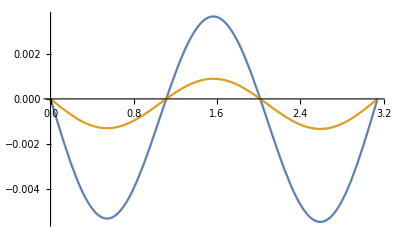

```mathematica
Plot[{λ6Bθ0p0Dressed[1,π/2,phi2],λ6Bθ0p0Undressed[1,π/2,phi2,0.0062]},{phi2,0,π}]
```

InterpolatingFunction::dmval: Input value {-0.118469,0,0.0000641782} lies outside the range of data in the interpolating function. Extrapolation will be used.

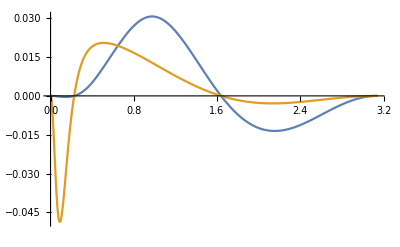

```mathematica
Plot[{λ6Bθ0p0Dressed[1,phi1,π/2],λ6Bθ0p0Undressed[1,phi1,π/2,0.0062]},{phi1,0,π}]
```

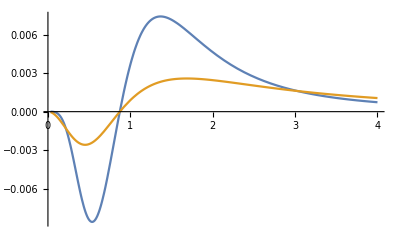

```mathematica
Plot[{λ6Bθ0p0Dressed[k,π/2,π/2],λ6Bθ0p0Undressed[k,π/2,π/2,0.0062]},{k,pmin,4},PlotRange->All]
```

```mathematica
NIntegrate[λ6Bθ0p0Dressed[k,phi1,phi2],{phi2,0,π},{phi1,0,π},{k,0.0001,10000}]
```

CompiledFunction::cfsa: Argument 0.761294+k^2-1.74496 k Cos[phi1]-0.00872485 k Cos[phi2] Sin[phi1] at position 1 should be a machine-size real number.

CompiledFunction::cfsa: Argument k^2 at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00641372 and 1.53971×10^-7 for the integral and error estimates.

-0.00641372

```mathematica
NIntegrate[λ6Bθ0p0Undressed[k,phi1,phi2,0.62],{phi2,0,π},{phi1,0,π},{k,0.0001,10000}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in k near {phi2,phi1,k} = {2.29498,0.0000149046,0.872499}. NIntegrate obtained 15.0114 and 0.436461 for the integral and error estimates.

15.0114

```mathematica
Plot3D[λ6p1p2θ[p1^2,p2^2,θmin],{p1,pmin,4},{p2,pmin,4}]
```

-Graphics3D-

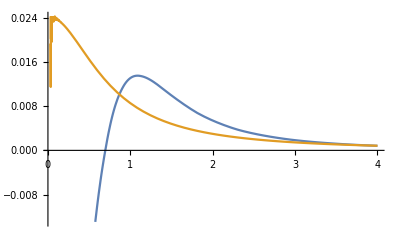

```mathematica
Plot[{λ6p1p2θ[p1^2,p1^2,θmin],-λ6X[p1,p1,θmin,0.62]},{p1,pmin,4}]
```

## λ7

### λ7

-Graphics-

```mathematica
λ7eucA=(-1/(16h[p1,p2]) (C5A+2*C7A))/.q->p1-p2/.Ruleλ/.RuleAng/.RuleEuc;
```

```mathematica
MyFortranForm[λ7eucA/.RuleFort1/.RuleFort2/.RuleFort3//Simplify,95,l7a]
```

l7a = (5.d-1*(Ca - 2.d0*Cf)*Dks*g**2*(Cosphi1*k*(Costh*p1 - p2) + Cosphi**2*p1*p2 + &
    & Cosphi1**2*p1*p2 + 2.d0*(-1.d0 + Costh**2)*p1*p2 + Cosphi*(- k*p1 + Costh*k*p2 - &
    & 2.d0*Cosphi1*Costh*p1*p2))*QAkpp1s*QAkpp2s*lambda1(kpp1s,kpp2s,ang12k)*lambda1(kpp2s,p2**2,an &
    & g2k)*lambda1(p1**2,kpp1s,ang1k))/((-1.d0 + Costh**2)*p1*p2*(k**2*QAkpp1s**2 + &
    & 2.d0*Cosphi1*k*p1*QAkpp1s**2 + p1**2*QAkpp1s**2 + QBkpp1s**2)*(k**2*QAkpp2s**2 + &
    & 2.d0*Cosphi*k*p2*QAkpp2s**2 + p2**2*QAkpp2s**2 + QBkpp2s**2))

```mathematica
λ7eucB=(-1/(16h[p1,p2]) (C5B+2*C7B))/.q->p1-p2/.Ruleλ/.RuleAng/.RuleEuc;
```

```mathematica
MyFortranForm[λ7eucB/.RuleFort1/.RuleFort2/.RuleFort3//Simplify,80,l7b]
```

l7b = (-5.d-1*Ca*Dkmp1s*Dkmp2s*g**2*k*(3.d0*Cosphi1**3*k**2*p1**2*p2 + &
    & 3.d0*Cosphi**3*k**2*p1*p2**2 + (-1.d0 + Costh**2)*k*p1*p2*(k**2 + Costh*p1*p2) &
    & + Cosphi**2*k*p2*(Cosphi1*k*p1*(1.1d1*p1 - 1.4000000000000001d1*Costh*p2) + &
    & k**2*(-9.d0*p1 + 6.d0*Costh*p2) + p1*(-4.d0*p1**2 + 3.d0*Costh*p1*p2 - &
    & 2.d0*p2**2)) + Cosphi1*(4.d0*k**4*p2 + 2.d0*p1**2*p2**3 - &
    & 2.d0*Costh*k**2*p1*(2.d0*k**2 + p1**2 + p2**2) - Costh**2*p1**2*p2*(3.d0*k**2 &
    & + 2.d0*p2**2) + k**2*p2*(5.d0*p1**2 + 2.d0*p2**2)) + &
    & Cosphi1**2*k*p1*(3.d0*Costh*p1*(2.d0*k**2 + p2**2) - p2*(9.d0*k**2 + &
    & 2.d0*p1**2 + 4.d0*p2**2)) + Cosphi*(-2.d0*(-1.d0 + Costh**2)*p1**3*p2**2 + &
    & 4.d0*k**4*(p1 - Costh*p2) - 6.d0*Cosphi1*k**3*(p1**2 - 3.d0*Costh*p1*p2 + &
    & p2**2) + k**2*(2.d0*p1**3 - 2.d0*(1.d0 + 7.d0*Cosphi1**2)*Costh*p1**2*p2 + &
    & (5.d0 + 1.1d1*Cosphi1**2 - 3.d0*Costh**2)*p1*p2**2 - 2.d0*Costh*p2**3) + &
    & 6.d0*Cosphi1*k*p1*p2*(-2.d0*p1*p2 + Costh**2*p1*p2 + Costh*(p1**2 + &
    & p2**2))))*QAks*lambda1(k**2,p2**2,phi)*lambda1(p1**2,k**2,phi1)*Lsg(k**2 + &
    & p1**2 - Costh*p1*p2 + p2**2 - k*(Cosphi1*p1 + Cosphi*p2)))/((-1.d0 + &
    & Costh**2)*kmp1s*kmp2s*p1*p2*(k**2*QAks**2 + QBks**2))

#### Imports:

Data λ7 in general kinematics, all ingredients at TL, for α = 0.47.

```mathematica
λ7p1p2θpertData=Import[".//Data_Lambdas_Perturbative/l7pert.dat"];
LogLogλ7p1p2θpertData=Interpolation[λ7p1p2θpertData,Method->"Hermite",InterpolationOrder->3];
λ7p1p2θpert[p12_,p22_,θ_]:=LogLogλ7p1p2θpertData[Log10[p12],Log10[p22],θ];
```

#### Plot:

Comparing perturbative results from the SDE, package X and Davydychev - soft-gluon:

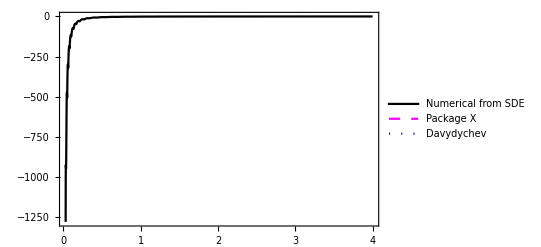
-Graphics-λ_7(p^2)p [GeV]

```mathematica
Quiet[Labeled[Show[Plot[{λ7p1p2θpert[x^2,x^2,θmin],λ7X[x,x,θmin,0.008],λ7Davy[x,x,π+θmin,0.008]}, {x,pmin, 4}, 

PlotStyle->{ Black,{Magenta,Dashed},{Blue,Dotted}}, PlotRange->All,

PlotLegends->Placed[ LineLegend[ {"Numerical from SDE","Package X","Davydychev"},LegendFunction->(Framed[#,FrameStyle->Black]&), LegendLayout->{"Column",1}, LabelStyle->Directive[Black,12] ] , {0.65, 0.7}]],  

Frame->True, BaseStyle->12, Axes->True, PlotRangePadding->None ], {"λ_7(p^2)", "p [GeV]"}, {Left, Bottom} , RotateLabel->True]]
```

Comparing perturbative results from the SDE, package X and Davydychev - symmetric:

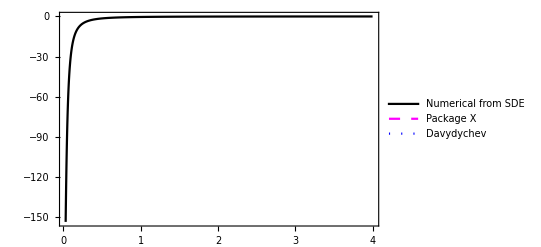
-Graphics-λ_7(p^2)p [GeV]

```mathematica
Quiet[Labeled[Show[Plot[{λ7p1p2θpert[x^2,pmin^2,θcommon],λ7X[x,pmin,θcommon,0.008],λ7Davy[x,pmin,2*θcommon,0.008]}, {x,pmin, 4}, 

PlotStyle->{ Black,{Magenta,Dashed},{Blue,Dotted}}, PlotRange->All, 

PlotLegends->Placed[ LineLegend[ {"Numerical from SDE","Package X","Davydychev"},LegendFunction->(Framed[#,FrameStyle->Black]&), LegendLayout->{"Column",1}, LabelStyle->Directive[Black,12] ] , {0.65, 0.7}]],  

Frame->True, BaseStyle->12, Axes->True, PlotRangePadding->None ], {"λ_7(p^2)", "p [GeV]"}, {Left, Bottom} , RotateLabel->True]]
```

Comparing perturbative results from the SDE, package X and Davydychev - general:

```mathematica
Quiet[Labeled[Show[Plot3D[{λ7p1p2θpert[x^2,y^2,θcommon],λ7X[x,y,θcommon,0.008],λ7Davy[x,y,2*θcommon,0.008]}, {x, pmin, 0.5},{y,pmin,0.5}, 

PlotStyle->{ Magenta,Orange,Blue}, PlotRange->All, 

PlotLegends->{"Numerical from SDE","Package X","Davydychev"}],

Frame->True, BaseStyle->12, Axes->True, PlotRangePadding->None ], {"λ_7(p_1^2,p_2^2,π/3)", "p_1 [GeV]","p_2 [GeV]"}, {Left, Bottom} , RotateLabel->True]]
```

-Graphics3D-λ_7(p_1^2,p_2^2,π/3)p_1 [GeV]p_2 [GeV]

## λ8

### λ8

-Graphics-

```mathematica
λ8eucA=(-1/(32h[p1,p2]^2)  (2h[p1,p2]C4A+3*q.q*C8A))/.q->p1-p2/.Ruleλ/.RuleAng/.RuleEuc;
```

```mathematica
MyFortranForm[λ8eucA/.RuleFort1/.RuleFort2/.RuleFort3//Simplify,95,l8a]
```

l8a = (2.5d-1*(Ca - 2.d0*Cf)*Dks*g**2*(- p2**2*QAkpp2s*QBkpp1s + &
    & 3.d0*Cosphi1**2*p2**2*QAkpp2s*QBkpp1s - p1**2*QAkpp1s*QBkpp2s + &
    & Cosphi1**2*p1**2*QAkpp1s*QBkpp2s - (-1.d0 + 3.d0*Cosphi1**2)*Costh*p1*p2*(QAkpp2s*QBkpp1s + &
    & QAkpp1s*QBkpp2s) - Costh**3*p1*p2*(QAkpp2s*QBkpp1s + QAkpp1s*QBkpp2s) + &
    & Costh**2*(p2**2*QAkpp2s*QBkpp1s + (1.d0 + 2.d0*Cosphi1**2)*p1**2*QAkpp1s*QBkpp2s) + &
    & Cosphi**2*(p2**2*QAkpp2s*QBkpp1s + 2.d0*Costh**2*p2**2*QAkpp2s*QBkpp1s + &
    & 3.d0*p1**2*QAkpp1s*QBkpp2s - 3.d0*Costh*p1*p2*(QAkpp2s*QBkpp1s + QAkpp1s*QBkpp2s)) + &
    & 2.d0*Cosphi*Cosphi1*(-3.d0*Costh*p2**2*QAkpp2s*QBkpp1s - 3.d0*Costh*p1**2*QAkpp1s*QBkpp2s + &
    & (1.d0 + 2.d0*Costh**2)*p1*p2*(QAkpp2s*QBkpp1s + &
    & QAkpp1s*QBkpp2s)))*lambda1(kpp1s,kpp2s,ang12k)*lambda1(kpp2s,p2**2,ang2k)*lambda1(p1**2,kpp1s &
    & ,ang1k))/((-1.d0 + Costh**2)**2*p1**2*p2**2*(k**2*QAkpp1s**2 + 2.d0*Cosphi1*k*p1*QAkpp1s**2 + &
    & p1**2*QAkpp1s**2 + QBkpp1s**2)*(k**2*QAkpp2s**2 + 2.d0*Cosphi*k*p2*QAkpp2s**2 + &
    & p2**2*QAkpp2s**2 + QBkpp2s**2))

```mathematica
λ8eucB=(-1/(32h[p1,p2]^2)  (2h[p1,p2]C4B+3*q.q*C8B))/.q->p1-p2/.Ruleλ/.RuleAng/.RuleEuc;
```

```mathematica
MyFortranForm[λ8eucB/.RuleFort1/.RuleFort2/.RuleFort3//Simplify,80,l8b]
```

l8b = (2.5d-1*Ca*Dkmp1s*Dkmp2s*g**2*(2.d0*Costh*(-1.d0 + &
    & Costh**2)**2*p1**3*p2**3 + k**4*((-1.d0 + 3.d0*Cosphi**2 + Cosphi1**2 - &
    & 6.d0*Cosphi*Cosphi1*Costh + Costh**2 + 2.d0*Cosphi1**2*Costh**2)*p1**2 + &
    & 2.d0*(2.d0*Cosphi*Cosphi1 + Costh - 3.d0*Cosphi**2*Costh - &
    & 3.d0*Cosphi1**2*Costh + 4.d0*Cosphi*Cosphi1*Costh**2 - Costh**3)*p1*p2 + &
    & (-1.d0 + 3.d0*Cosphi1**2 - 6.d0*Cosphi*Cosphi1*Costh + Costh**2 + &
    & Cosphi**2*(1.d0 + 2.d0*Costh**2))*p2**2) - 2.d0*(-1.d0 + &
    & Costh**2)*k*p1**2*p2**2*(Cosphi1*(-1.d0 + 3.d0*Costh**2)*p1 - &
    & 2.d0*Cosphi1*Costh*p2 + Cosphi*(-2.d0*Costh*p1 - p2 + 3.d0*Costh**2*p2)) + &
    & k**2*p1*p2*(2.d0*(1.d0 + 2.d0*Cosphi1**2)*p1*p2 - 2.d0*(1.d0 + &
    & 5.d0*Cosphi1**2)*Costh**2*p1*p2 + Costh**3*(p1**2 + 6.d0*Cosphi1**2*p1**2 + &
    & p2**2) - Costh*(p1**2 + 3.d0*Cosphi1**2*p1**2 + p2**2 - 3.d0*Cosphi1**2*p2**2) &
    & - 2.d0*Cosphi*Cosphi1*((-2.d0 + 5.d0*Costh**2)*p1**2 + (-2.d0 + &
    & 5.d0*Costh**2)*p2**2 + p1*(2.d0*Costh*p2 - 8.d0*Costh**3*p2)) + &
    & Cosphi**2*(4.d0*p1*p2 - 1.d1*Costh**2*p1*p2 + 6.d0*Costh**3*p2**2 + &
    & 3.d0*Costh*(p1**2 - p2**2))) - k**3*(Cosphi1**3*p1*((1.d0 + &
    & 2.d0*Costh**2)*p1**2 - 6.d0*Costh*p1*p2 + 3.d0*p2**2) + Cosphi*p2*(3.d0*(1.d0 &
    & + Cosphi**2 - Costh**2)*p1**2 + 2.d0*Costh*(-1.d0 - 3.d0*Cosphi**2 + &
    & Costh**2)*p1*p2 + (-1.d0 + Cosphi**2 + Costh**2 + &
    & 2.d0*Cosphi**2*Costh**2)*p2**2) + Cosphi1*((-1.d0 + 3.d0*Cosphi**2 + &
    & Costh**2)*p1**3 + 2.d0*Costh*(-1.d0 - 6.d0*Cosphi**2 + Costh**2)*p1**2*p2 + &
    & (3.d0 - 3.d0*Costh**2 + 5.d0*Cosphi**2*(1.d0 + 2.d0*Costh**2))*p1*p2**2 - &
    & 6.d0*Cosphi**2*Costh*p2**3) + Cosphi*Cosphi1**2*(5.d0*p1**2*p2 + &
    & 1.d1*Costh**2*p1**2*p2 + 3.d0*p2**3 - 6.d0*Costh*(p1**3 + &
    & 2.d0*p1*p2**2))))*QBks*lambda1(k**2,p2**2,phi)*lambda1(p1**2,k**2,phi1)*Lsg(k* &
    & *2 + p1**2 - Costh*p1*p2 + p2**2 - k*(Cosphi1*p1 + Cosphi*p2)))/((-1.d0 + &
    & Costh**2)**2*kmp1s*kmp2s*p1**2*p2**2*(k**2*QAks**2 + QBks**2))